## Introduction

This notebook applies my notebook "Semisimple Lie Algebras.nb" to various symmetry groups important in physics. The ones I'll cover here are space-time geometry, particle symmetries, and some extras.

Details are in each section and its subsection.

This notebook uses representation symmetrized powers: plethysms. They are displayed as a list of
* Multiplicity
* Symmetry types as a “Young diagram” displayed as small boxes
* Counted list of irreps with that symmetry type

All-horizontal boxes mean full symmetry, and all-vertical boxes mean full antisymmetry,
and the decompositions are in order (full symmetry) to (full antisymmetry).

An interesting mixed-symmetry case is for the fourth power: a 2*2 set of boxes in its Young diagram. It is the symmetry of the Riemann curvature tensor.

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Semisimple Lie Algebras.nb"]
```

### Setup

The function ShowIrrepListProperties[type, maxwtlist] outputs a list of these values for each irrep in the list:
* Its highest weight (how it is specified)
* Its dimension or degeneracy
* Reality: 0 = real, 1 = pseudoreal, -1 = complex
* Moduli for the conserved quantities / congruence values
* Those conserved quantities / congruence values

Reality:
* 0 = real: Self-conjugate; Lie-algebra matrices can be turned into real ones
* 1 = pseudoreal: Self-conjugate; those matrices cannot
* -1 = complex: Not self-conjugate; those matrices cannot

The function ShowLabeledIrrepListProperties[labels,type, maxwtlist] has an additional member of each row: each of the labels.

```mathematica
ShowIrreps[type_,maxwtlist_] := Table[GetRep[type,maxwtlist[[k]]],{k,Length[maxwtlist]}]
```

```mathematica
ShowIrrepProperties[type_,maxwts_] := Join[{maxwts,TotalDegen[type,maxwts]},RepProperties[type,maxwts]]
```

```mathematica
ShowIrrepListProperties[type_,maxwtlist_] := ShowIrrepProperties[type,#]& /@ maxwtlist
```

```mathematica
ShowLabeledIrrepListProperties[labels_,type_,maxwtlist_] := Transpose[Prepend[Transpose[ShowIrrepListProperties[type,maxwtlist]],labels]]
```

```mathematica
ShowAlgProdIrrepProperties[tplist_,maxwts_] := Module[{mwproper,tpmx,tw,tp,mw,dgns,props},
mwproper = Take[maxwts,Length[tplist]];
tpmx = Transpose[{tplist,mwproper}];
dgns = Table[{tp,mw} = tw;
TotalDegen[tp,mw],
{tw,tpmx}];
props = Table[{tp,mw} = tw;
RepProperties[tp,mw],
{tw,tpmx}];
{maxwts,Times @@ dgns,dgns,props}
]
```

```mathematica
ShowAlgProdIrrepListProperties[tplist_,maxwtlist_] := ShowAlgProdIrrepProperties[tplist,#]& /@ maxwtlist
```

```mathematica
ShowLabeledAlgProdIrrepListProperties[labels_,tplist_,maxwtlist_] := Transpose[Prepend[Transpose[ShowAlgProdIrrepListProperties[tplist,maxwtlist]],labels]]
```

## Representation Symmetrized Powers - Plethysms

### Setup

```mathematica
YDGSize = 12;
```

```mathematica
YDGraph[yd_] := Graphics[{EdgeForm[Black],FaceForm[None],Table[Translate[Rectangle[],{j-1,-(i-1)}],{i,Length[yd]},{j,yd[[i]]}]},ImageSize->YDGSize*{Max[yd],Length[yd]}]
```

```mathematica
YDToIrrep[yd_] := Reverse[Differences[Reverse[Append[yd,0]]]]
```

```mathematica
(* Args are the rep-power decomposition, the power, and whether to show the A(n) irrep for the Young diagram *)
```

```mathematica
AddRepPowerAnnot[decomp_,pwr_,ShowYDIrrep_]:= Module[{dgrmlist,mults,yds},
dgrmlist = GetTensorPowerYDX[pwr]["DgrmList"];
If[Length[dgrmlist]==0,dgrmlist = {{1,{},1,1}}];
mults = YDGetMultiplicities[dgrmlist];
yds =YDGetRepDiagrams[dgrmlist];
Transpose[{mults,YDGraph /@ yds,If[ShowYDIrrep,(YDToIrrep /@ yds),Nothing], decomp}]
]
```

```mathematica
(* The labeling is multiplicity, Young diagram as a diagram, and if ShowYDIrrep is true, the YD's associated A(n) irrep. *)
```

```mathematica
DecomposeRepPowerLabeled[type_,maxwts_,pwr_,ShowYDIrrep_:False] := AddRepPowerAnnot[DecomposeRepPower[type,maxwts,pwr],pwr,ShowYDIrrep]
```

```mathematica
DecomposeRepPowerXtndLabeled[type_,xttype_,maxwts_,pwr_,ShowYDIrrep_:False] := AddRepPowerAnnot[DecomposeRepPowerXtnd[type,xttype,maxwts,pwr],pwr,ShowYDIrrep]
```

```mathematica
DecomposeAlgProdRepPowerLabeled[tplist_,maxwts_,pwr_,ShowYDIrrep_:False] := AddRepPowerAnnot[DecomposeAlgProdRepPower[tplist,maxwts,pwr],pwr,ShowYDIrrep]
```

```mathematica
DecomposeAlgProdRepPowerXtndLabeled[tplist_,xttype_,maxwts_,pwr_,ShowYDIrrep_:False] := AddRepPowerAnnot[DecomposeAlgProdRepPowerXtnd[tplist,xttype,maxwts,pwr],pwr,ShowYDIrrep]
```

### Examples

Representation powers are decomposed by symmetry class, and each symmetry class has:
* Multiplicity
* “Young diagram” as boxes
* A(n) irrep associated with that Young diagram

Here, the powers are demonstrated on the fundamental irrep of an A(n) algebra.

```mathematica
rpwrgen[n_] := {{1,n},PadRight[{1},n]}
```

```mathematica
{rpwralg,rpwrrep} = rpwrgen[5]
```

{{1,5},{1,0,0,0,0}}

```mathematica
DecomposeRepPowerLabeled[rpwralg,rpwrrep,0,True]
```

{{1,-Graphics-,{},{{1,{0,0,0,0,0}}}}}

```mathematica
DecomposeRepPowerLabeled[rpwralg,rpwrrep,1,True]
```

{{1,-Graphics-,{1},{{1,{1,0,0,0,0}}}}}

```mathematica
DecomposeRepPowerLabeled[rpwralg,rpwrrep,2,True]
```

{{1,-Graphics-,{2},{{1,{2,0,0,0,0}}}},{1,-Graphics-,{0,1},{{1,{0,1,0,0,0}}}}}

```mathematica
DecomposeRepPowerLabeled[rpwralg,rpwrrep,3,True]
```

{{1,-Graphics-,{3},{{1,{3,0,0,0,0}}}},{2,-Graphics-,{1,1},{{1,{1,1,0,0,0}}}},{1,-Graphics-,{0,0,1},{{1,{0,0,1,0,0}}}}}

```mathematica
DecomposeRepPowerLabeled[rpwralg,rpwrrep,4,True]
```

{{1,-Graphics-,{4},{{1,{4,0,0,0,0}}}},{3,-Graphics-,{2,1},{{1,{2,1,0,0,0}}}},{2,-Graphics-,{0,2},{{1,{0,2,0,0,0}}}},{3,-Graphics-,{1,0,1},{{1,{1,0,1,0,0}}}},{1,-Graphics-,{0,0,0,1},{{1,{0,0,0,1,0}}}}}

## Space-Time Geometry

Has space and time in several dimensions.

3D -- for quantum-mechanical angular momentum

All the others come in pairs. The first of the pair is the transverse dimensions of the second of the pair, the dimensions of the second one without the two light-cone dimensions. This is because the degrees of freedom of a massless particle field are in those transverse dimensions.

Familiar space-time:
2D: transverse: helicity (projection of spin on direction of motion)
4D: full

Superstring space-time:
8D: transverse
10D: full

M-theory space-time:
9D: transverse
11D: full

Though the full space-time algebras are SO(3,1), SO(9,1), and SO(10,1), they are analytic continuations of SO(4), SO(10), and SO(11), and the representation theory of the latter algebras carries over into the former algebras.

Kinds of elementary-particle fields:
Standard Model and supersymmetric extensions: scalar (spin 0), spinor (spin 1/2), vector (spin 1)
Gravity: symmetric 2-tensor (spin 2) graviton
Supergravity (supersymmetric gravity): gravity with a vector-spinor (spin 3/2) gravitino

Higher-dimensional supergravities often have extra fields.

### 3D -- QM angular momentum -- SO(3) ~ SU(2)

This is from the ladder-operator formulation of angular momentum in quantum mechanics. It is the smallest simple nonabelian algebra: A1 ~ B1 ~ C1 -- SU(2) ~ SO(3) ~ Sp(2)

Angular momentum = highest root = (1/2) * (highest weight)

This algebra has a conjugacy class, the spinor parity: whether the angular momentum is integer or half-odd, equivalent to whether the highest weight is even or odd.

Angular momentum 0: scalar, 1/2: spinor, 1: vector, 3/2: vector-spinor, 2: 2-tensor
Lists are of (label, multiplicity/degeneracy, root vector, weight vector)

Symm = symmetric: T(j,i) = T(i,j) for indices i,j
Trclss = traceless: sum over i of T(i,i) = 0

```mathematica
spc3 = {1,1};
```

```mathematica
MatrixForm /@ ShowIrreps[spc3,Table[{2j},{j,0,2,1/2}]]
```

{(1 | {0} | {0}),(1 | {1/2} | {1}
1 | {-1/2} | {-1}),(1 | {1} | {2}
1 | {0} | {0}
1 | {-1} | {-2}),(1 | {3/2} | {3}
1 | {1/2} | {1}
1 | {-1/2} | {-1}
1 | {-3/2} | {-3}),(1 | {2} | {4}
1 | {1} | {2}
1 | {0} | {0}
1 | {-1} | {-2}
1 | {-2} | {-4})}

```mathematica
Range[0,2,1/2]
```

{0,1/2,1,3/2,2}

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Spinor","Vector","Vector-Spinor","Symm Trclss 2-Tensor"},spc3,Table[{2j},{j,0,2,1/2}]]  // MatrixForm
```

(Scalar | {0} | 1 | 1 | {2} | {0}
Spinor | {1} | 2 | -1 | {2} | {1}
Vector | {2} | 3 | 1 | {2} | {0}
Vector-Spinor | {3} | 4 | -1 | {2} | {1}
Symm Trclss 2-Tensor | {4} | 5 | 1 | {2} | {0})

```mathematica
(* Spins 1/2,1/2 -> spins 1, 0 *)
DecomposeRepProduct[spc3,{1},{1}] // MatrixForm
```

(1 | {2}
1 | {0})

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{1},2]
```

{matthr[{1,-Graphics-,{{1,{2}}}}],matthr[{1,-Graphics-,{{1,{0}}}}]}

```mathematica
(* Spins 1,1/2 -> spins 3/2, 1/2 *)DecomposeRepProduct[spc3,{2},{1}] // MatrixForm
```

(1 | {3}
1 | {1})

```mathematica
(* Spins 1, -> spins 2, 1, 0 *)DecomposeRepProduct[spc3,{2},{2}] // MatrixForm
```

(1 | {4}
1 | {2}
1 | {0})

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{2},2]
```

{matthr[{1,-Graphics-,{{1,{4}},{1,{0}}}}],matthr[{1,-Graphics-,{{1,{2}}}}]}

```mathematica
(* The symmetric one is a 2-tensor that decomposes into a symmetric and traceless 2-tensor (spin 2) and the trace, a scalar (spin 0). The antisymmetric one is a vector, the cross product. *)
```

```mathematica
(* Set of three spins 1/2 *)
```

```mathematica
DecomposeRepProdList[spc3,{{1},{1},{1}}] // MatrixForm
```

(1 | {3}
2 | {1})

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{1},3]
```

{matthr[{1,-Graphics-,{{1,{3}}}}],matthr[{2,-Graphics-,{{1,{1}}}}],matthr[{1,-Graphics-,{}}]}

```mathematica
(* Set of three spins 1 *)
```

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{2},3]
```

{matthr[{1,-Graphics-,{{1,{6}},{1,{2}}}}],matthr[{2,-Graphics-,{{1,{4}},{1,{2}}}}],matthr[{1,-Graphics-,{{1,{0}}}}]}

```mathematica
(* Set of four spins 1/2 *)
```

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{1},4]
```

{matthr[{1,-Graphics-,{{1,{4}}}}],matthr[{3,-Graphics-,{{1,{2}}}}],matthr[{2,-Graphics-,{{1,{0}}}}],matthr[{3,-Graphics-,{}}],matthr[{1,-Graphics-,{}}]}

```mathematica
(* Set of four spins 1 *)
```

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc3,{2},4]
```

{matthr[{1,-Graphics-,{{1,{8}},{1,{4}},{1,{0}}}}],matthr[{3,-Graphics-,{{1,{6}},{1,{4}},{1,{2}}}}],matthr[{2,-Graphics-,{{1,{4}},{1,{0}}}}],matthr[{3,-Graphics-,{{1,{2}}}}],matthr[{1,-Graphics-,{}}]}

```mathematica
(* The middle one, the 2*2 one, is for the Riemann tensor, and it has the same symmetry as the Ricci tensor (symmetric square) *)
```

### 2D -- Transverse 4D -- Helicity -- SO(2) ~ U(1)

Helicity: spin projected onto direction of motion. helrep[h_] gives both directions if nonzero as a counted list.

```mathematica
helrep[h_] := If[h!=0,{{1,{h}},{1,{-h}}},{{1,{0}}}]
```

```mathematica
vec2 = helrep[1];  (* Vector *)
```

```mathematica
spn2 =helrep[1/2];  (* Spinor *)
```

```mathematica
vcsp2 = helrep[3/2]; (* Vector-spinor: gravitino *)
```

```mathematica
(* Vector + spinor = vector-spinor + spinor *)
```

```mathematica
MatrixForm @ DecomposeAlgProdRepProductXtnd[{},"Cntd",vec2,"Cntd",spn2]
```

(1 | {3/2}
1 | {1/2}
1 | {-1/2}
1 | {-3/2})

```mathematica
(* Powers of vector rep *)
```

```mathematica
matthr[x_] := MatrixForm /@ x
```

```mathematica
(* 1: that rep itself *)
```

```mathematica
matthr /@  DecomposeAlgProdRepPowerXtndLabeled[{},"Cntd",vec2,1]
```

{{1,-Graphics-,(1 | {1}
1 | {-1})}}

```mathematica
(* 2: (2,0), (0)*)
```

```mathematica
matthr/@  DecomposeAlgProdRepPowerXtndLabeled[{},"Cntd",vec2,2]
```

{{1,-Graphics-,(1 | {2}
1 | {0}
1 | {-2})},{1,-Graphics-,(1 | {0})}}

```mathematica
(* The first one is symmetric, and it contains a symmetric traceless part (graviton) and a trace (scalar: 0) *)
```

```mathematica
MatrixForm[Reverse[Sort[Join[helrep[2],helrep[0]]]]]
```

(1 | {2}
1 | {0}
1 | {-2})

```mathematica
(* The second one is antisymmetric, and is for the 2-index antisymmetric symbol, a scalar in 2D *)
```

```mathematica
MatrixForm[helrep[0]]
```

(1 | {0})

```mathematica
(* 3: (3,1), (1), () *)
```

```mathematica
matthr /@  DecomposeAlgProdRepPowerXtndLabeled[{},"Cntd",vec2,3]
```

{{1,-Graphics-,(1 | {3}
1 | {1}
1 | {-1}
1 | {-3})},{2,-Graphics-,(1 | {1}
1 | {-1})},{1,-Graphics-,{}}}

```mathematica
(* 4: (4,2,0), (2,0), (0), (), () *)
```

```mathematica
matthr /@  DecomposeAlgProdRepPowerXtndLabeled[{},"Cntd",vec2,4]
```

{{1,-Graphics-,(1 | {4}
1 | {2}
1 | {0}
1 | {-2}
1 | {-4})},{3,-Graphics-,(1 | {2}
1 | {0}
1 | {-2})},{2,-Graphics-,(1 | {0})},{3,-Graphics-,{}},{1,-Graphics-,{}}}

```mathematica
(* The middle one, the 2*2 one, is for the Riemann tensor, and it is a scalar *)
```

### 4D -- SO(4) ~ SO(3) * SO(3)

This algebra is not simple but composite, with two SO(3) parts, handled like the SO(3) discussed earlier: a pair of angular momenta j1,j2 with highest weight {2j1,2j2}. It has two congruency classes, one for each part, both working like SO(3) ones.

The antisymmetric 2-tensors and the Weyl-like 4-tensors have self-duality decompositions into two parts, and those parts are indicated as 1 and 2.

Weyl-like tensors are traceless Riemann-like ones, and Riemann-like ones are antisymmetric on the first two and last two indices and symmetric on those two indices as pairs,  with the sum over permutations of the first three indices vanishing.
Riemann-like: T(j,i,k,l) = - T(i,j,k,l), T(k,l,i,j) = T(i,j,k,l), T(i,j,k,l)+T(j,k,i,l)+T(k,i,j,l) = 0
Weyl-like: Riemann-like with sum over j of T(i,j,k,j) = 0

```mathematica
spc4 ={4,2};
```

```mathematica
spc4irreps = {{0,0}, {1,0}, {0,1}, {1,1}, {2,1},{1,2}, {2,0},{0,2},{2,2},{4,0},{0,4}};
```

```mathematica
MatrixForm /@ ShowIrreps[spc4,Take[spc4irreps,4]]
```

{(1 | {0,0} | {0,0}),(1 | {1/2,0} | {1,0}
1 | {-1/2,0} | {-1,0}),(1 | {0,1/2} | {0,1}
1 | {0,-1/2} | {0,-1}),(1 | {1/2,1/2} | {1,1}
1 | {-1/2,1/2} | {-1,1}
1 | {1/2,-1/2} | {1,-1}
1 | {-1/2,-1/2} | {-1,-1})}

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Spinor 1","Spinor 2","Vector","Vector-Spinor 1","Vector-Spinor 2","Antisymm 2-Tensor 1","Antisymm 2-Tensor 2","Symm Trclss 2-Tensor","Weyl-like Tensor 1","Weyl-like Tensor 2"},spc4,spc4irreps] //  MatrixForm
```

(Scalar | {0,0} | 1 | 1 | {2,2,2} | {0,0,0}
Spinor 1 | {1,0} | 2 | 0 | {2,2,2} | {1,1,0}
Spinor 2 | {0,1} | 2 | 0 | {2,2,2} | {1,0,1}
Vector | {1,1} | 4 | 1 | {2,2,2} | {0,1,1}
Vector-Spinor 1 | {2,1} | 6 | 0 | {2,2,2} | {1,0,1}
Vector-Spinor 2 | {1,2} | 6 | 0 | {2,2,2} | {1,1,0}
Antisymm 2-Tensor 1 | {2,0} | 3 | 0 | {2,2,2} | {0,0,0}
Antisymm 2-Tensor 2 | {0,2} | 3 | 0 | {2,2,2} | {0,0,0}
Symm Trclss 2-Tensor | {2,2} | 9 | 1 | {2,2,2} | {0,0,0}
Weyl-like Tensor 1 | {4,0} | 5 | 0 | {2,2,2} | {0,0,0}
Weyl-like Tensor 2 | {0,4} | 5 | 0 | {2,2,2} | {0,0,0})

```mathematica
(* Vector squared *)
matthr /@ DecomposeRepPowerLabeled[spc4,{1,1},2]
```

{{1,-Graphics-,(1 | {2,2}
1 | {0,0})},{1,-Graphics-,(1 | {0,2}
1 | {2,0})}}

```mathematica
(* Traceless 2-tensor, scalar; two antisymmetric tensors. *)
```

```mathematica
(* Vector * Spinor: spinor, vector-spinor *)DecomposeRepProduct[spc4,{1,1},{0,1}] // MatrixForm
```

(1 | {1,2}
1 | {1,0})

```mathematica
(* Vector cubed *)
matthr /@ DecomposeRepPowerLabeled[spc4,{1,1},3]
```

{{1,-Graphics-,(1 | {3,3}
1 | {1,1})},{2,-Graphics-,(1 | {1,3}
1 | {3,1}
1 | {1,1})},{1,-Graphics-,(1 | {1,1})}}

```mathematica
(* Vector to fourth power *)
matthr /@ DecomposeRepPowerLabeled[spc4,{1,1},4]
```

{{1,-Graphics-,(1 | {4,4}
1 | {2,2}
1 | {0,0})},{3,-Graphics-,(1 | {2,4}
1 | {4,2}
1 | {2,2}
1 | {0,2}
1 | {2,0})},{2,-Graphics-,(1 | {0,4}
1 | {2,2}
1 | {4,0}
1 | {0,0})},{3,-Graphics-,(1 | {2,2}
1 | {0,2}
1 | {2,0})},{1,-Graphics-,(1 | {0,0})}}

```mathematica
(* The middle one, the 2*2 one, is for the Riemann tensor, and it is the Ricci tensor {2,2}+{0,0} plus the Weyl tensor {4,0}+{0,4} *)
```

### 8D -- Transverse 10D -- SO(8)

From string theory: transverse degrees of freedom.

There are five types of superstring, based on three types of 10D supergravity:
N = 1: Type I, HO, HE
Bosonic part: (vector)*(vector) = (graviton: symmetric traceless 2-tensor) + (antisymmetric 2-tensor) + (dilaton: scalar)
Fermionic part: (vector)*(spinor 1) = (gravitino: vector-spinor 1) + (spinor 2)

N = 2: Types IIA, IIB
They have N = 1 with additional bosonic and fermionic parts:
Type IIA
Bosonic part: (spinor 1)*(spinor 2) = (vector) + (antisymmetric 3-tensor)
Fermionic part: (vector)*(spinor 2) = (vector-spinor 2) + (spinor 1)
Type IIB
Bosonic part: (spinor 1)*(spinor 1) = (scalar) + (antisymmetric 2-tensor) + ((anti)-self-dual part of antisymmetric 4-tensor)
Fermionic part: (vector)*(spinor 1) = (vector-spinor 1) + (spinor 2)

```mathematica
spc8 ={4,4};
```

```mathematica
spc8irreps = {{0,0,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0},{2,0,0,0},{1,0,1,0},{1,0,0,1},{0,0,1,1},{0,0,2,0},{0,0,0,2}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor 1","Spinor 2","Antisymm 2-Tensor","Symm Trclss 2-Tensor","Vector-spinor 1","Vector-spinor 2","Antisymm 3-Tensor","Antisymm 4-Tensor 1","Antisymm 4-Tensor 2"},spc8,spc8irreps] // MatrixForm
```

(Scalar | {0,0,0,0} | 1 | 1 | {2,2,2} | {0,0,0}
Vector | {1,0,0,0} | 8 | 1 | {2,2,2} | {0,1,1}
Spinor 1 | {0,0,1,0} | 8 | 0 | {2,2,2} | {1,1,0}
Spinor 2 | {0,0,0,1} | 8 | 0 | {2,2,2} | {1,0,1}
Antisymm 2-Tensor | {0,1,0,0} | 28 | 1 | {2,2,2} | {0,0,0}
Symm Trclss 2-Tensor | {2,0,0,0} | 35 | 1 | {2,2,2} | {0,0,0}
Vector-spinor 1 | {1,0,1,0} | 56 | 0 | {2,2,2} | {1,0,1}
Vector-spinor 2 | {1,0,0,1} | 56 | 0 | {2,2,2} | {1,1,0}
Antisymm 3-Tensor | {0,0,1,1} | 56 | 1 | {2,2,2} | {0,1,1}
Antisymm 4-Tensor 1 | {0,0,2,0} | 35 | 0 | {2,2,2} | {0,0,0}
Antisymm 4-Tensor 2 | {0,0,0,2} | 35 | 0 | {2,2,2} | {0,0,0})

Supergravity multiplets:
N = 1
Bosonic: 64
Symmetric traceless 2-tensor: 35, antisymmetric 2-tensor: 28, scalar: 1
Fermionic: 64
Vector-spinor: 56, spinor: 8

N = 2 IIA extras:
Bosonic: 64
Vector: 8, antisymmetric 3-tensor: 56
Fermionic: 64
(like N = 1 fermionic)

N = 2 IIB extras:
Bosonic: 64
Scalar: 1, antisymmetric 2-tensor: 28, one-half of antisymmetric 4-tensor: 35
Fermionic: 64
(like N = 1 fermionic)

```mathematica
(* Vector * vector ecomposes into symmetric traceless, adjoint, and scalar *)
matthr /@ DecomposeRepPowerLabeled[spc8,{1,0,0,0},2]
```

{{1,-Graphics-,(1 | {2,0,0,0}
1 | {0,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0})}}

```mathematica
(* Vector * spinor ecomposes into vector-spinor and other spinor *)
DecomposeRepProduct[spc8,{1,0,0,0},{0,0,1,0}] // MatrixForm
```

(1 | {1,0,1,0}
1 | {0,0,0,1})

```mathematica
(* Other vector-spinor *)
DecomposeRepProduct[spc8,{1,0,0,0},{0,0,0,1}] // MatrixForm
```

(1 | {1,0,0,1}
1 | {0,0,1,0})

```mathematica
(* Product of the two spinors *)
DecomposeRepProduct[spc8,{0,0,1,0},{0,0,0,1}]
```

{{1,{0,0,1,1}},{1,{1,0,0,0}}}

```mathematica
(* Square of spinor *)
DecomposeRepPowerLabeled[spc8,{0,0,1,0},2]
```

{{1,-Graphics-,{{1,{0,0,2,0}},{1,{0,0,0,0}}}},{1,-Graphics-,{{1,{0,1,0,0}}}}}

```mathematica
(* Square of other spinor *)
DecomposeRepPowerLabeled[spc8,{0,0,0,1},2]
```

{{1,-Graphics-,{{1,{0,0,0,2}},{1,{0,0,0,0}}}},{1,-Graphics-,{{1,{0,1,0,0}}}}}

```mathematica
Table[{k,MatrixForm @ DecomposeRepPwrSym[spc8,{1,0,0,0},k,-1]},{k,1,4}]
```

{{1,(1 | {1,0,0,0})},{2,(1 | {0,1,0,0})},{3,(1 | {0,0,1,1})},{4,(1 | {0,0,0,2}
1 | {0,0,2,0})}}

```mathematica
(* Compactification: breakdown of 10D into 6D * 4D. The latter has the light cone, making it effectively 2D.
Results are multiplets in the 6 dimensions - SO(6) - and the helicity in 4D - U(1) *)
spc8d62 = MakeRootDemoter[{4,4},1];spc8d62["Subtypes"]
```

{{4,3}}

```mathematica
(* Vector makes vector with zero helicity, and sscalar with helicity +- 1 *)
DoBranching[spc8d62,{1,0,0,0}] // MatrixForm
```

(1 | {{1,0,0},0}
1 | {{0,0,0},1}
1 | {{0,0,0},-1})

```mathematica
(* Spinor becomes two spinors, each with a separate helicity of 1/2 or -1/2 *)
DoBranching[spc8d62,{0,0,1,0}] // MatrixForm
```

(1 | {{0,1,0},1/2}
1 | {{0,0,1},-1/2})

```mathematica
(* Like the earlier spinor, but flipped *)
DoBranching[spc8d62,{0,0,0,1}] // MatrixForm
```

(1 | {{0,0,1},1/2}
1 | {{0,1,0},-1/2})

```mathematica
(* Antisymmetric 2-tensor (adjoint) becomes antisymmetric 2-tensor with zero helicity, vectors with helicities +- 1, and a scalar with zero helicity *)
DoBranching[spc8d62,{0,1,0,0}] // MatrixForm
```

(1 | {{1,0,0},1}
1 | {{0,1,1},0}
1 | {{1,0,0},-1}
1 | {{0,0,0},0})

```mathematica
(* Symmetric traceless 2-tensor becomes symmetric traceless 2-tensor with zero helicity, vectors with helicities +- 1, and scalars with helicities +- 2 *)
DoBranching[spc8d62,{2,0,0,0}] // MatrixForm
```

(1 | {{2,0,0},0}
1 | {{1,0,0},1}
1 | {{0,0,0},2}
1 | {{1,0,0},-1}
1 | {{0,0,0},0}
1 | {{0,0,0},-2})

```mathematica
(* Vector-spinors branch into vector-spinors and plain spinors. The plain-spinor parts have helicities +-1/2 and +-3/2, the vector-spinor parts only helicities +-1/2 *)
DoBranching[spc8d62,{1,0,1,0}] // MatrixForm
```

(1 | {{1,1,0},1/2}
1 | {{0,1,0},3/2}
1 | {{1,0,1},-1/2}
1 | {{0,0,1},1/2}
1 | {{0,1,0},-1/2}
1 | {{0,0,1},-3/2})

```mathematica
(* Antisymmetric 3-tensor becomes a vector with zero helicity, antisymmetric 2-tensors with helicity +- 1, and an antisymmetric 3-tensor with zero helicity *)
DoBranching[spc8d62,{0,0,1,1}] // MatrixForm
```

(1 | {{0,1,1},1}
1 | {{0,0,2},0}
1 | {{0,2,0},0}
1 | {{1,0,0},0}
1 | {{0,1,1},-1})

```mathematica
(* Antisymmetric 4-tensor part becomes an antisymmetric 2-tensor with zero helicity, and an antisymmetric 3-tensor with each part having helicity 1 or -1 *)
DoBranching[spc8d62,{0,0,2,0}] // MatrixForm
```

(1 | {{0,2,0},1}
1 | {{0,1,1},0}
1 | {{0,0,2},-1})

```mathematica
(* Like the earlier antisymmetric 4-tensor part, but flipped *)DoBranching[spc8d62,{0,0,0,2}] // MatrixForm
```

(1 | {{0,0,2},1}
1 | {{0,1,1},0}
1 | {{0,2,0},-1})

### 10D -- SO(10)

From string theory.

```mathematica
spc10 = {4,5};
```

```mathematica
spc10irreps = {{0,0,0,0,0},{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0},{2,0,0,0,0},{1,0,0,1,0},{1,0,0,0,1}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor 1","Spinor 2","Antisymm 2-Tensor","Symm Trclss 2-tensor","Vector-spinor 1","Vector-spinor 2"},spc10,spc10irreps] // MatrixForm
```

(Scalar | {0,0,0,0,0} | 1 | 1 | {2,4} | {0,0}
Vector | {1,0,0,0,0} | 10 | 1 | {2,4} | {0,2}
Spinor 1 | {0,0,0,1,0} | 16 | 0 | {2,4} | {1,1}
Spinor 2 | {0,0,0,0,1} | 16 | 0 | {2,4} | {1,3}
Antisymm 2-Tensor | {0,1,0,0,0} | 45 | 1 | {2,4} | {0,0}
Symm Trclss 2-tensor | {2,0,0,0,0} | 54 | 1 | {2,4} | {0,0}
Vector-spinor 1 | {1,0,0,1,0} | 144 | 0 | {2,4} | {1,3}
Vector-spinor 2 | {1,0,0,0,1} | 144 | 0 | {2,4} | {1,1})

Supergravity multiplets:
N = 1
Bosonic: 64
Symmetric traceless 2-tensor: 35, antisymmetric 2-tensor: 28, scalar: 1
Fermionic: 64
Vector-spinor: 56, spinor: 8

(not sure about N = 2)

```mathematica
(* Vector * vector ecomposes into symmetric traceless 2-tensor, antisymmetric 2-tensor, and scalar *)
matthr /@ DecomposeRepPowerLabeled[spc10,{1,0,0,0,0},2]
```

{{1,-Graphics-,(1 | {2,0,0,0,0}
1 | {0,0,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0,0})}}

```mathematica
(* Vector * spinor ecomposes into vector-spinor and spinor *)
DecomposeRepProduct[spc10,{1,0,0,0,0},{0,0,0,1,0}] // MatrixForm
```

(1 | {1,0,0,1,0}
1 | {0,0,0,0,1})

```mathematica
(* Compactification: breakdown of 10D into 6D * 4D. *)
spc10d64 = MakeExtensionSplitter[{4,5},3]; spc10d64["Subtypes"]
```

{{4,3},{4,2}}

```mathematica
(* Vector makes (vector, scalar) and (scalar, vector) *)
DoBranching[spc10d64,{1,0,0,0,0}] // MatrixForm
```

(1 | {{1,0,0},{0,0}}
1 | {{0,0,0},{1,1}})

```mathematica
(* Spinor 1 becomes (spinor 1, spinor 1) and (spinor 2, spinor 2) *)
DoBranching[spc10d64,{0,0,0,1,0}] // MatrixForm
```

(1 | {{0,1,0},{1,0}}
1 | {{0,0,1},{0,1}})

```mathematica
(* Spinor 2 becomes (spinor 1, spinor 2) and (spinor 2, spinor 1) *)
DoBranching[spc10d64,{0,0,0,0,1}] // MatrixForm
```

(1 | {{0,1,0},{0,1}}
1 | {{0,0,1},{1,0}})

```mathematica
(* Antisymmetric 2-tensor (adjoint) becomes (AS 2-T (adj), scalar), (scalar, AS 2-T (adj)), and (vector,vector) *)
DoBranching[spc10d64,{0,1,0,0,0}] // MatrixForm
```

(1 | {{1,0,0},{1,1}}
1 | {{0,1,1},{0,0}}
1 | {{0,0,0},{0,2}}
1 | {{0,0,0},{2,0}})

```mathematica
(* Symmetric traceless tensor becomes (Sym TL 2-T, scalar), (scalar, Sym TL 2-T), (vector,vector), and (scalar, scalar) *)
DoBranching[spc10d64,{2,0,0,0,0}] // MatrixForm
```

(1 | {{2,0,0},{0,0}}
1 | {{1,0,0},{1,1}}
1 | {{0,0,0},{2,2}}
1 | {{0,0,0},{0,0}})

```mathematica
(* Vector-spinor 1 becomes (vector-spinor 1, spinor 1), (vector-spinor 2, spinor 2), (spinor 1, vector-spinor 1), (spinor 2, vector-spinor 2), (spinor 1, spinor 2), and (spinor 2, spinor 1) *)
DoBranching[spc10d64,{1,0,0,1,0}] // MatrixForm
```

(1 | {{1,1,0},{1,0}}
1 | {{1,0,1},{0,1}}
1 | {{0,1,0},{2,1}}
1 | {{0,0,1},{1,2}}
1 | {{0,1,0},{0,1}}
1 | {{0,0,1},{1,0}})

```mathematica
(* Vector-spinor 1 becomes (vector-spinor 1, spinor 2), (vector-spinor 2, spinor 1), (spinor 1, vector-spinor 2), (spinor 2, vector-spinor 1), (spinor 1, spinor 1), and (spinor 2, spinor 2) *)
DoBranching[spc10d64,{1,0,0,0,1}] // MatrixForm
```

(1 | {{1,1,0},{0,1}}
1 | {{1,0,1},{1,0}}
1 | {{0,1,0},{1,2}}
1 | {{0,0,1},{2,1}}
1 | {{0,1,0},{1,0}}
1 | {{0,0,1},{0,1}})

### 9D -- Transverse 11D -- SO(9)

From M-theory: transverse degrees of freedom.

```mathematica
spc9 = {2,4};
```

```mathematica
spc9irreps = {{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{2,0,0,0},{0,0,1,0},{1,0,0,1}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor","Antisymm 2-Tensor","Symm Trclss 2-Tensor","Antisymm 3-Tensor","Vector-Spinor"},spc9,spc9irreps] // MatrixForm
```

(Scalar | {0,0,0,0} | 1 | 1 | {2} | {0}
Vector | {1,0,0,0} | 9 | 1 | {2} | {0}
Spinor | {0,0,0,1} | 16 | 1 | {2} | {1}
Antisymm 2-Tensor | {0,1,0,0} | 36 | 1 | {2} | {0}
Symm Trclss 2-Tensor | {2,0,0,0} | 44 | 1 | {2} | {0}
Antisymm 3-Tensor | {0,0,1,0} | 84 | 1 | {2} | {0}
Vector-Spinor | {1,0,0,1} | 128 | 1 | {2} | {1})

Supergravity multiplet
Bosonic: 128
Symm Trclss 2-Tensor: 44, Antisymm 3-tensor: 84
Fermionic: 128
Vector-Spinor: 128

```mathematica
(* Vector * vector ecomposes into symmetric traceless 2-tensor, antisymmetric 2-tensor, and scalar *)
matthr /@ DecomposeRepPowerLabeled[spc9,{1,0,0,0},2]
```

{{1,-Graphics-,(1 | {2,0,0,0}
1 | {0,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0})}}

```mathematica
(* Vector * antisymmetric 2-tensor: includes vector, antisymmetric 3-tensor *)
DecomposeRepProduct[spc9,{1,0,0,0},{0,1,0,0}] // MatrixForm
```

(1 | {1,1,0,0}
1 | {0,0,1,0}
1 | {1,0,0,0})

```mathematica
matthr /@ DecomposeRepPowerLabeled[spc9,{1,0,0,0},3]
```

{{1,-Graphics-,(1 | {3,0,0,0}
1 | {1,0,0,0})},{2,-Graphics-,(1 | {1,1,0,0}
1 | {1,0,0,0})},{1,-Graphics-,(1 | {0,0,1,0})}}

```mathematica
(* Vector * spinor ecomposes into vector-spinor and spinor *)
DecomposeRepProduct[spc9,{1,0,0,0},{0,0,0,1}] // MatrixForm
```

(1 | {1,0,0,1}
1 | {0,0,0,1})

```mathematica
(* Go from M-theory to string theory: 9D -> 8D + 1D *)
spc9d8 = MakeExtensionSplitter[{2,4},4];spc9d8["Subtypes"]
```

{{4,4}}

```mathematica
(* Vector -> vector + scalar *)
DoBranching[spc9d8,{1,0,0,0}] // MatrixForm
```

(1 | {{1,0,0,0}}
1 | {{0,0,0,0}})

```mathematica
(* Spinor -> two spinors *)
DoBranching[spc9d8,{0,0,0,1}] // MatrixForm
```

(1 | {{0,0,1,0}}
1 | {{0,0,0,1}})

```mathematica
(* Antisymmetric 2-tensor -> antisymmetric 2-tensor, vector *)
DoBranching[spc9d8,{0,1,0,0}] // MatrixForm
```

(1 | {{0,1,0,0}}
1 | {{1,0,0,0}})

```mathematica
(* Symmetric traceless tensor -> symmetric traceless 2-tensor, vector, scalar *)
DoBranching[spc9d8,{2,0,0,0}] // MatrixForm
```

(1 | {{2,0,0,0}}
1 | {{1,0,0,0}}
1 | {{0,0,0,0}})

```mathematica
(* Antisymmetric 3-tensor -> antisymmetric 3-tensor, antisymmetric 2-tensor *)
DoBranching[spc9d8,{0,0,1,0}] // MatrixForm
```

(1 | {{0,0,1,1}}
1 | {{0,1,0,0}})

```mathematica
(* Vector-spinor -> 2 vector-spinors, 2 spinors *)
DoBranching[spc9d8,{1,0,0,1}] // MatrixForm
```

(1 | {{1,0,1,0}}
1 | {{1,0,0,1}}
1 | {{0,0,1,0}}
1 | {{0,0,0,1}})

### 11D -- SO(11)

From M-theory.

```mathematica
spc11 = {2,5};
```

```mathematica
spc11irreps = {{0,0,0,0,0},{1,0,0,0,0},{0,0,0,0,1},{0,1,0,0,0},{2,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor","Antisymm 2-Tensor","Symm Trclss 2-Tensor","Antisymm 3-Tensor","Vector-Spinor"},spc11,spc11irreps] // MatrixForm
```

(Scalar | {0,0,0,0,0} | 1 | 1 | {2} | {0}
Vector | {1,0,0,0,0} | 11 | 1 | {2} | {0}
Spinor | {0,0,0,0,1} | 32 | -1 | {2} | {1}
Antisymm 2-Tensor | {0,1,0,0,0} | 55 | 1 | {2} | {0}
Symm Trclss 2-Tensor | {2,0,0,0,0} | 65 | 1 | {2} | {0}
Antisymm 3-Tensor | {0,0,1,0,0} | 165 | 1 | {2} | {0}
Vector-Spinor | {1,0,0,0,1} | 320 | -1 | {2} | {1})

Supergravity multiplet
Bosonic: 128
Symm Trclss 2-Tensor: 44, Antisymm 3-tensor: 84
Fermionic: 128
Vector-Spinor: 128

```mathematica
(* Vector * vector ecomposes into symmetric traceless, antisymmetric/adjoint, and scalar *)
matthr /@ DecomposeRepPowerLabeled[spc11,{1,0,0,0,0},2]
```

{{1,-Graphics-,(1 | {2,0,0,0,0}
1 | {0,0,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0,0})}}

```mathematica
(* Vector * adjoint: includes vector, antisymmetric 3-tensor *)
DecomposeRepProduct[spc11,{1,0,0,0,0},{0,1,0,0,0}] // MatrixForm
```

(1 | {1,1,0,0,0}
1 | {0,0,1,0,0}
1 | {1,0,0,0,0})

```mathematica
(* Vector * spinor ecomposes into vector-spinor and spinor *)
DecomposeRepProduct[spc11,{1,0,0,0,0},{0,0,0,0,1}] // MatrixForm
```

(1 | {1,0,0,0,1}
1 | {0,0,0,0,1})

```mathematica
(* Go from M-theory to string theory: 11D -> 10D + 1D *)
spc11d10 = MakeExtensionSplitter[{2,5},5];spc11d10["Subtypes"]
```

{{4,5}}

```mathematica
(* Vector -> vector + scalar *)
DoBranching[spc11d10,{1,0,0,0,0}] // MatrixForm
```

(1 | {{1,0,0,0,0}}
1 | {{0,0,0,0,0}})

```mathematica
(* Spinor -> two spinors *)
DoBranching[spc11d10,{0,0,0,0,1}] // MatrixForm
```

(1 | {{0,0,0,1,0}}
1 | {{0,0,0,0,1}})

```mathematica
(* Antisymmetric tensor -> antisymmetric tensor, vector *)
DoBranching[spc11d10,{0,1,0,0,0}] // MatrixForm
```

(1 | {{0,1,0,0,0}}
1 | {{1,0,0,0,0}})

```mathematica
(* Symmetric traceless tensor -> symmetric traceless tensor, vector, scalar *)
DoBranching[spc11d10,{2,0,0,0,0}] // MatrixForm
```

(1 | {{2,0,0,0,0}}
1 | {{1,0,0,0,0}}
1 | {{0,0,0,0,0}})

```mathematica
(* Antisymmetric 3-tensor -> antisymmetric 3-tensor, antisymmetric/adjoint *)
DoBranching[spc11d10,{0,0,1,0,0}] // MatrixForm
```

(1 | {{0,0,1,0,0}}
1 | {{0,1,0,0,0}})

```mathematica
(* Vector-spinor -> 2 vector-spinors, 2 spinors *)
DoBranching[spc11d10,{1,0,0,0,1}] // MatrixForm
```

(1 | {{1,0,0,1,0}}
1 | {{1,0,0,0,1}}
1 | {{0,0,0,1,0}}
1 | {{0,0,0,0,1}})

## Gauge and Flavor Symmetry

Turning to  particle symmetries, I consider gauge flavor ones.

The simplest particle symmetry is U(1), associated with adding a complex phase with a particle without mixing it with other kinds of particles. Electromagnetism has a U(1) gauge symmetry, and flavor conservation laws, like of baryon and lepton number, have U(1) symmetries associated with them.

The next sort is SU(2), which acts like 3D angular momentum, thus the flavor symmetry “isospin” from “isotopic spin”. The unbroken Standard Model has a SU(2) symmetry called “weak isospin”, for up-like quarks vs. down-like ones and neutrinos vs. electron-like leptons. Plain isospin is an approximate flavor symmetry between up and down quarks, which are much less massive than hadrons. It is respected by the strong / QCD interaction, but not by the electromagnetic or weak interactions.

The next one is SU(3), the QCD (quantum chromodynamics) gauge symmetry, and an approximate flavor symmetry for the three lightest quarks: up, down, and strange. The flavor one is somewhat broken by the strange quark’s mass, so I illustrate its breaking into SU(2) * U(1) -- isospin and hypercharge (average electric charge of an isospin multiplet).

This is followed by some GUT ones: Georgi-Glashow SU(5), Pati-Salam SU(4) * SU(2) * SU(2) or SO(6) * SO(4), and SO(10), SU(3)^3, E(6), and E(8) models. The latter one is part of the E(8) * E(8) gauge symmetry in the HE heterotic superstring, one of the five kinds.

### QCD Gauge Symmetry and Light-Quark Flavor Symmetry: SU(3)

They are treated together here because they have the same symmetry group.

The “interesting” irreps here:
Quark color (red, green, blue) / flavor (up, down, strange)
Quark anticolor / antiflavor
Gluon color-anticolor / 3-(anti)color / flavor-antiflavor / 3-(anti)flavor octet
3-flavor decuplet
3-antiflavor decuplet

```mathematica
gfssu3 = {1,2};
```

```mathematica
gfssu3irreps = {{0,0},{1,0},{0,1},{1,1},{3,0},{0,3}};
```

```mathematica
MatrixForm /@ ShowIrreps[gfssu3,gfssu3irreps]
```

{(1 | {0,0} | {0,0}),(1 | {2/3,1/3} | {1,0}
1 | {-1/3,1/3} | {-1,1}
1 | {-1/3,-2/3} | {0,-1}),(1 | {1/3,2/3} | {0,1}
1 | {1/3,-1/3} | {1,-1}
1 | {-2/3,-1/3} | {-1,0}),(1 | {1,1} | {1,1}
1 | {0,1} | {-1,2}
1 | {1,0} | {2,-1}
2 | {0,0} | {0,0}
1 | {-1,0} | {-2,1}
1 | {0,-1} | {1,-2}
1 | {-1,-1} | {-1,-1}),(1 | {2,1} | {3,0}
1 | {1,1} | {1,1}
1 | {0,1} | {-1,2}
1 | {1,0} | {2,-1}
1 | {-1,1} | {-3,3}
1 | {0,0} | {0,0}
1 | {-1,0} | {-2,1}
1 | {0,-1} | {1,-2}
1 | {-1,-1} | {-1,-1}
1 | {-1,-2} | {0,-3}),(1 | {1,2} | {0,3}
1 | {1,1} | {1,1}
1 | {0,1} | {-1,2}
1 | {1,0} | {2,-1}
1 | {0,0} | {0,0}
1 | {1,-1} | {3,-3}
1 | {-1,0} | {-2,1}
1 | {0,-1} | {1,-2}
1 | {-1,-1} | {-1,-1}
1 | {-2,-1} | {-3,0})}

```mathematica
ShowLabeledIrrepListProperties[{"Singlet","Triplet","Anti-triplet","Octet","Decuplet","Anti-decuplet"},gfssu3,gfssu3irreps] // MatrixForm
```

(Singlet | {0,0} | 1 | 1 | {3} | {0}
Triplet | {1,0} | 3 | 0 | {3} | {1}
Anti-triplet | {0,1} | 3 | 0 | {3} | {2}
Octet | {1,1} | 8 | 1 | {3} | {0}
Decuplet | {3,0} | 10 | 0 | {3} | {0}
Anti-decuplet | {0,3} | 10 | 0 | {3} | {0})

Mesons -- octet (flavor), singlet (color, flavor)

```mathematica
DecomposeRepProduct[gfssu3,{1,0},{0,1}] // MatrixForm
```

(1 | {1,1}
1 | {0,0})

Baryons -- flavor: decuplet (spin-3/2), two octets (spin-1/2) / color: singlet

```mathematica
matthr /@ DecomposeRepPowerLabeled[gfssu3,{1,0},2]
```

{{1,-Graphics-,(1 | {2,0})},{1,-Graphics-,(1 | {0,1})}}

Antibaryons -- antiflavor: decuplet (spin-3/2), two octets (spin-1/2) / anticolor: singlet

```mathematica
matthr /@ DecomposeRepPowerLabeled[gfssu3,{0,1},2]
```

{{1,-Graphics-,(1 | {0,2})},{1,-Graphics-,(1 | {1,0})}}

```mathematica
spnsu2 = {1,1};
```

Decomposition of spin and flavor together for a 3-quark system.

The observed states are symmetric (spin-3/2 decuplet, spin-1/2 octet) rather than antisymmetric (spin-3/2 singlet, spin-1/2 octet), which is contrary to what one expects from Fermi-Dirac elementary-particle statistics, from quarks’ spin of 1/2.

```mathematica
matthr /@ DecomposeAlgProdRepPowerLabeled[{spnsu2,gfssu3},{{1},{1,0}},3]
```

{{1,-Graphics-,(1 | {{3},{3,0}}
1 | {{1},{1,1}})},{2,-Graphics-,(1 | {{3},{1,1}}
1 | {{1},{3,0}}
1 | {{1},{1,1}}
1 | {{1},{0,0}})},{1,-Graphics-,(1 | {{1},{1,1}}
1 | {{3},{0,0}})}}

Decomposition of spin, flavor, and color together with Fermi-Dirac statistics: antisymmetry. Note that when the last part is antisymmetry {0,0} the rest of it is what one finds in the observed baryons: a spin-3/2 decuplet and a spin 1/2 octet.

```mathematica
MatrixForm @ DecomposeAlgProdRepPwrSym[{spnsu2,gfssu3,gfssu3},{{1},{1,0},{1,0}},3,-1]
```

(1 | {{3},{1,1},{1,1}}
1 | {{1},{3,0},{1,1}}
1 | {{1},{1,1},{3,0}}
1 | {{3},{3,0},{0,0}}
1 | {{1},{1,1},{1,1}}
1 | {{3},{0,0},{3,0}}
1 | {{1},{1,1},{0,0}}
1 | {{1},{0,0},{1,1}})

### Separation of Up/Down from Strange Quarks: SU(3) -> SU(2) * U(1)

Decomposes three-quark flavor SU(3) into:
- Isospin: up and down: SU(2)
- Hypercharge: up/down and strange: U(1)

```mathematica
fssu3d2 = BrancherRearrangeU1s[MakeRootDemoter[{1,2},2],{{1/2}}]; fssu3d2["Subtypes"]
```

{{1,1}}

```mathematica
su3replocs[maxwts_] := (#[[2]]& /@ GetRep[{1,2},maxwts]).CanonicalRootVectors[{1,2},2].DiagonalMatrix[{1,-1}]
```

```mathematica
su3pttext[maxwts_,lbls_] := Text @@@ Transpose[{Style[#,Medium]& /@ lbls,su3replocs[maxwts]}]
```

Quark
u,d - (1/2,1/6)
s - (0,-1/3)

```mathematica
DoBranching[fssu3d2,{1,0}] // MatrixForm
```

(1 | {{1},1/6}
1 | {{0},-1/3})

```mathematica
Graphics[su3pttext[{1,0},{"u","d","s"}],ImageSize->Tiny]
```

-Graphics-

Antiquark
u*,d* - (1/2,-1/6)
s* - (0,1/3)

```mathematica
DoBranching[fssu3d2,{0,1}] // MatrixForm
```

(1 | {{0},1/3}
1 | {{1},-1/6})

```mathematica
Graphics[su3pttext[{0,1},{"s*","d*","u*"}],ImageSize->Tiny]
```

-Graphics-

Quark-antiquark or 3-(anti)quark octet
pion - sigma - antisigma - (1,0)
kaon - xi - antinucleon - (1/2,-1/2)
kaon - nucleon - antixi - (1/2,1/2)
eta - lambda - antilambda - (0,0)

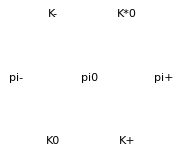
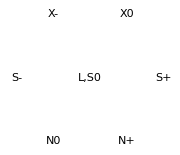
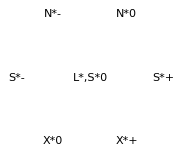

```mathematica
Graphics[su3pttext[{1,1},#],ImageSize->Small]& /@ {{"K+","K0","pi+","pi0","pi-","K*0","K-"},{"N+","N0","S+","L,S0","S-","X0","X-"},{"X*+","X*0","S*+","L*,S*0","S*-","N*0","N*-"}}
```

```mathematica
DoBranching[fssu3d2,{1,1}] // MatrixForm
```

(1 | {{1},1/2}
1 | {{2},0}
1 | {{0},0}
1 | {{1},-1/2})

Three-quark decuplet
delta - (3/2,1/2)
sigma-x - (1,0)
xi-x - (1/2,-1/2)
omega - (0,-1)

```mathematica
DoBranching[fssu3d2,{3,0}] // MatrixForm
```

(1 | {{3},1/2}
1 | {{2},0}
1 | {{1},-1/2}
1 | {{0},-1})

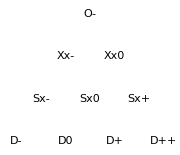

```mathematica
Graphics[su3pttext[{3,0},{"D++","D+","D0","Sx+","D-","Sx0","Sx-","Xx0","Xx-","O-"}],ImageSize->Small]
```

Three-antiquark decuplet
antidelta - (3/2,-1/2)
antisigma-x - (1,0)
antixi-x - (1/2,1/2)
antiomega - (0,1)

```mathematica
DoBranching[fssu3d2,{0,3}] // MatrixForm
```

(1 | {{0},1}
1 | {{1},1/2}
1 | {{2},0}
1 | {{3},-1/2})

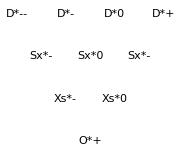

```mathematica
Graphics[su3pttext[{0,3},{"O*+","Xs*0","Xs*-","Sx*-","Sx*0","D*+","Sx*-","D*0","D*-","D*--"}],ImageSize->Small]
```

### The Standard Model and GUT’s: Algebras and Multiplets

The multiplets are displayed as a list with entries:
Label
Multiplet highest weights, including U(1) factors
Total degeneracy, with individual degeneracies for the Standard Model
{Rep reality, congruence moduli, congruence values}, a list for the Standard Model

GH = GUT Higgs

#### (Minimal Supersymmetric) Standard Model

The Standard Model of elementary particle physics has gauge symmetry
SU(3) * SU(2) * U(1)
with gauge-field content
SU(3) - color field - gluon - quantum chromodynamics (QCD)
SU(2) - weak-isospin field - W
U(1) - weak-hypercharge field - B
The second and third ones are collectively the electroweak interaction

The irreps are for the Minimal Supersymmetric Standard Model, with its pair of Higgs doublets.
The labels are:
EF = elementary fermion, H = Higgs particle, G = gauge particle
L = left-handed, R = right-handed
Q = quark doublet, U = up-quark singlet, D = down-quark singlet, L = lepton doublet, N = neutrino, E = electron, Hu = up Higgs, Hd = down Higgs (distinct in the MSSM)

QCD states:
{0,0} - singlet - real - congruence 0 / 3
{1,0} - triplet - complex - congruence 1 / 3 - colors: red, green, blue
{0,1} - triplet - complex - congruence 2 / 3 - anticolors: cyan, magenta, yellow
{1,0} - octet - real - congruence 0 / 3 - adjoint - color-anticolor combinations

WIS states:
{w} - WIS value w/2 - real if w is even, pseudoreal if w is odd - congruence mod(w,2) / 2

I will not discuss elementary particles’ masses, since there is no good theory of them, nothing comparable to the gauge symmetries.

```mathematica
gssm = {{1,2},{1,1}};
```

```mathematica
gssmirreps = {{{0,0},{0},0},{{1,0},{1},1/6},{{0,1},{1},-1/6},{{0,1},{0},-2/3},{{1,0},{0},2/3},{{0,1},{0},1/3},{{1,0},{0},-1/3},{{0,0},{1},-1/2},{{0,0},{1},1/2},{{0,0},{0},0},{{0,0},{0},0},{{0,0},{0},1},{{0,0},{0},-1},{{0,0},{1},1/2},{{0,0},{1},-1/2},{{0,0},{1},-1/2},{{0,0},{1},1/2},{{1,1},{0},0},{{0,0},{2},0},{{0,0},{0},0}};
```

```mathematica
ShowLabeledAlgProdIrrepListProperties[{"Singlet","EF L Q","EF R Q*","EF L U*","EF R U","EF L D*","EF R D","EF L L","EF R L*","EF L N*","EF R N","EF L E*","EF R E","H L Hu","H R Hu*","H L Hd","H R Hd*","G Gluon","G W","G B"},gssm,gssmirreps] // MatrixForm
```

(Singlet | {{0,0},{0},0} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}}
EF L Q | {{1,0},{1},1/6} | 6 | {3,2} | {{0,{3},{1}},{-1,{2},{1}}}
EF R Q* | {{0,1},{1},-1/6} | 6 | {3,2} | {{0,{3},{2}},{-1,{2},{1}}}
EF L U* | {{0,1},{0},-2/3} | 3 | {3,1} | {{0,{3},{2}},{1,{2},{0}}}
EF R U | {{1,0},{0},2/3} | 3 | {3,1} | {{0,{3},{1}},{1,{2},{0}}}
EF L D* | {{0,1},{0},1/3} | 3 | {3,1} | {{0,{3},{2}},{1,{2},{0}}}
EF R D | {{1,0},{0},-1/3} | 3 | {3,1} | {{0,{3},{1}},{1,{2},{0}}}
EF L L | {{0,0},{1},-1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
EF R L* | {{0,0},{1},1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
EF L N* | {{0,0},{0},0} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}}
EF R N | {{0,0},{0},0} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}}
EF L E* | {{0,0},{0},1} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}}
EF R E | {{0,0},{0},-1} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}}
H L Hu | {{0,0},{1},1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
H R Hu* | {{0,0},{1},-1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
H L Hd | {{0,0},{1},-1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
H R Hd* | {{0,0},{1},1/2} | 2 | {1,2} | {{1,{3},{0}},{-1,{2},{1}}}
G Gluon | {{1,1},{0},0} | 8 | {8,1} | {{1,{3},{0}},{1,{2},{0}}}
G W | {{0,0},{2},0} | 3 | {1,3} | {{1,{3},{0}},{1,{2},{0}}}
G B | {{0,0},{0},0} | 1 | {1,1} | {{1,{3},{0}},{1,{2},{0}}})

```mathematica
MakeStandardModelGraph[] := Module[{pdata,pdxi,pdx,size=0.1,plverts,handno,handleft,handright,labels},
(* QCD, WIS, WHC, chirality *)
pdata = {{0,0,0,0},{-1,0,1/3,1},{1,0,2/3,-1},{0,0,1,1},{1,1/2,1/6,1},{0,1/2,1/2,-1},{0,1,0,0}};
(* Do reflections by weak hypercharge, then weak isospin *)
pdxi = Flatten[If[#[[3]]!=0,{#,{-1,1,-1,-1}*#},{#}]& /@ pdata,1];
pdx =  Flatten[If[#[[2]]!=0,{#,{1,-1,1,1}*#},{#}]& /@ pdxi,1];
handno = Disk[{0,0},(2/3)size];
plverts = size*{{-3/4,0},{3/4,-Sqrt[3]/2},{3/4,Sqrt[3]/2}};
handleft = Scale[Polygon[plverts],{-1,1}];
handright = Scale[handleft,{-1,1}];
labels = {"X 0","D 1/3","D* -1/3","U 2/3","U* -2/3","E* +1","E -1","Q +2/3","Q -1/3","Q* -1/3","Q* -2/3","L* +1","L* 0","L 0","L -1","W +1","W -1"};
pdx = Transpose[Append[Transpose[pdx],labels]];
Graphics[Translate[{Switch[#[[1]],1,Lighter[Red,0.75],-1,Darker[Cyan,0],0,Lighter[Gray,0.75]],Switch[#[[4]],1,handright,-1,handleft,0,handno],Black,Style[Text[#[[5]]],Small]},#[[{3,2}]]]& /@ pdx]
]
```

```mathematica
(* Shows electric charge of each SM particle *)
```

```mathematica
MakeStandardModelGraph[]
```

-Graphics-

The Higgs particles have these interactions with the elementary fermions:
Hu . Q . U* - up quarks
Hd . Q . D* - down quarks
Hu . L . N* - neutrinos
Hd . L . E* - electrons
Left-handed ones; the right-handed ones are analogous

Tests of whether these interaction terms make singlets, as they ought to.

```mathematica
DecomposeAlgProdThreeRep[tplist_,maxwts1_,maxwts2_,maxwts3_] := DecomposeAlgProdRepProductXtnd[tplist,"Cntd",DecomposeAlgProdRepProduct[tplist,maxwts1,maxwts2],"Sngl",maxwts3]
```

```mathematica
(* Hu - Q - U* *)
```

```mathematica
DecomposeAlgProdThreeRep[gssm,{{0,0},{1},1/2},{{1,0},{1},1/6},{{0,1},{0},-2/3}] // MatrixForm
```

(1 | {{1,1},{2},0}
1 | {{1,1},{0},0}
1 | {{0,0},{2},0}
1 | {{0,0},{0},0})

```mathematica
(* Hd - Q - D* *)
```

```mathematica
DecomposeAlgProdThreeRep[gssm,{{0,0},{1},-1/2},{{1,0},{1},1/6},{{0,1},{0},1/3}] // MatrixForm
```

(1 | {{1,1},{2},0}
1 | {{1,1},{0},0}
1 | {{0,0},{2},0}
1 | {{0,0},{0},0})

```mathematica
(* Hu - L - N* *)
```

```mathematica
DecomposeAlgProdThreeRep[gssm,{{0,0},{1},1/2},{{0,0},{1},-1/2},{{0,0},{0},0}] // MatrixForm
```

(1 | {{0,0},{2},0}
1 | {{0,0},{0},0})

```mathematica
(* Hd - L - E* *)
```

```mathematica
DecomposeAlgProdThreeRep[gssm,{{0,0},{1},-1/2},{{0,0},{1},-1/2},{{0,0},{0},1}] // MatrixForm
```

(1 | {{0,0},{2},0}
1 | {{0,0},{0},0})

#### SU(5) - Georgi-Glashow

```mathematica
gssu5 = {1,4};
```

```mathematica
gssu5irreps = {{0,0,0,0},{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,0,0,1}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Singlet","EF R 5","EF L 10","EF R 10*","EF L 5*","H L 5","H R 5*","H L 5*","H R 5","Gauge"},gssu5,gssu5irreps] // MatrixForm
```

(Singlet | {0,0,0,0} | 1 | 1 | {5} | {0}
EF R 5 | {1,0,0,0} | 5 | 0 | {5} | {1}
EF L 10 | {0,1,0,0} | 10 | 0 | {5} | {2}
EF R 10* | {0,0,1,0} | 10 | 0 | {5} | {3}
EF L 5* | {0,0,0,1} | 5 | 0 | {5} | {4}
H L 5 | {1,0,0,0} | 5 | 0 | {5} | {1}
H R 5* | {0,0,0,1} | 5 | 0 | {5} | {4}
H L 5* | {0,0,0,1} | 5 | 0 | {5} | {4}
H R 5 | {1,0,0,0} | 5 | 0 | {5} | {1}
Gauge | {1,0,0,1} | 24 | 1 | {5} | {0})

The elementary-fermion irreps are antisymmetric powers of the fundamental one:
0: 1, 1: 5, 2: 10, 3: 10*, 4: 5*, 5: 1

```mathematica
Table[{k, MatrixForm @ DecomposeRepPwrSym[gssu5,{1,0,0,0},k,-1]},{k,0,5}] // MatrixForm
```

(0 | (1 | {0,0,0,0})
1 | (1 | {1,0,0,0})
2 | (1 | {0,1,0,0})
3 | (1 | {0,0,1,0})
4 | (1 | {0,0,0,1})
5 | (1 | {0,0,0,0}))

Higgs interactions

```mathematica
DecomposeThreeRep[type_,maxwts1_,maxwts2_,maxwts3_] := DecomposeRepProductXtnd[type,"Cntd",DecomposeRepProduct[type,maxwts1,maxwts2],"Sngl",maxwts3]
```

EF 10, EF 5*, H 5*
EF 10, EF 10, H 5
EF 1, EF 5*, H 5
All left-handed; right-handed is analogous

```mathematica
DecomposeThreeRep[gssu5,{0,1,0,0},{0,0,0,1},{0,0,0,1}] // MatrixForm
```

(1 | {0,1,0,2}
1 | {0,1,1,0}
2 | {1,0,0,1}
1 | {0,0,0,0})

```mathematica
DecomposeThreeRep[gssu5,{0,1,0,0},{0,1,0,0},{1,0,0,0}] // MatrixForm
```

(1 | {1,2,0,0}
1 | {2,0,1,0}
2 | {0,1,1,0}
2 | {1,0,0,1}
1 | {0,0,0,0})

```mathematica
DecomposeThreeRep[gssu5,{0,0,0,0},{0,0,0,1},{1,0,0,0}] // MatrixForm
```

(1 | {1,0,0,1}
1 | {0,0,0,0})

```mathematica
(* Making the adjoint *)
```

```mathematica
MatrixForm @ DecomposeRepProduct[gssu5,{1,0,0,0},{0,0,0,1}] // MatrixForm
```

(1 | {1,0,0,1}
1 | {0,0,0,0})

SU(5) GUT Higgs multiplets:
5, 5* - fundamental
24 - adjoint
15, 15* (for right-handed neutrinos) -- symmetric 2-tensor
https://www-zeuthen.desy.de/~blumlein/Talks/GUT.pdf

```mathematica
gssu5higgs= {{1,0,0,0},{0,0,0,1},{1,0,0,1},{2,0,0,0},{0,0,0,2}};
```

```mathematica
ShowIrrepListProperties[gssu5,gssu5higgs] // MatrixForm
```

({1,0,0,0} | 5 | 0 | {5} | {1}
{0,0,0,1} | 5 | 0 | {5} | {4}
{1,0,0,1} | 24 | 1 | {5} | {0}
{2,0,0,0} | 15 | 0 | {5} | {2}
{0,0,0,2} | 15 | 0 | {5} | {3})

```mathematica
(* Square decomposed by symmetry *)
```

```mathematica
matthr /@ DecomposeRepPowerLabeled[gssu5,{1,0,0,0},2]
```

{{1,-Graphics-,(1 | {2,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0})}}

#### SO(10) - Fritzsch-Minkowski-Georgi

```mathematica
gsso10 = {4,5};
```

```mathematica
gsso10irreps = {{0,0,0,0,0},{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor 1","Spinor 2","Adjoint"},gsso10,gsso10irreps] // MatrixForm
```

(Scalar | {0,0,0,0,0} | 1 | 1 | {2,4} | {0,0}
Vector | {1,0,0,0,0} | 10 | 1 | {2,4} | {0,2}
Spinor 1 | {0,0,0,1,0} | 16 | 0 | {2,4} | {1,1}
Spinor 2 | {0,0,0,0,1} | 16 | 0 | {2,4} | {1,3}
Adjoint | {0,1,0,0,0} | 45 | 1 | {2,4} | {0,0})

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Vector","Spinor 1","Spinor 2","Adjoint"},gsso10,gsso10irreps] // MatrixForm
```

(Scalar | {0,0,0,0,0} | 1 | 1 | {2,4} | {0,0}
Vector | {1,0,0,0,0} | 10 | 1 | {2,4} | {0,2}
Spinor 1 | {0,0,0,1,0} | 16 | 0 | {2,4} | {1,1}
Spinor 2 | {0,0,0,0,1} | 16 | 0 | {2,4} | {1,3}
Adjoint | {0,1,0,0,0} | 45 | 1 | {2,4} | {0,0})

SO(10) GUT Higgs 
10 - vector
45 - antisymmetric 2-tensor
54 - symmetric traceless 2-tensor
120 - antisymmetric 3-tensor
210 - antisymmetric 4-tensor
126, 126* - antisymmetric 5-tensor decomposed by self-duality

From
[hep-ph/0405300] SO(10) Group Theory for the Unified Model Building
https://arxiv.org/abs/hep-ph/0405300

```mathematica
gsso10higgs = {{1,0,0,0,0},{0,1,0,0,0},{2,0,0,0,0},{0,0,1,0,0},{0,0,0,2,0},{0,0,0,0,2},{0,0,0,1,1}};
```

```mathematica
ShowIrrepListProperties[gsso10,gsso10higgs] // MatrixForm
```

({1,0,0,0,0} | 10 | 1 | {2,4} | {0,2}
{0,1,0,0,0} | 45 | 1 | {2,4} | {0,0}
{2,0,0,0,0} | 54 | 1 | {2,4} | {0,0}
{0,0,1,0,0} | 120 | 1 | {2,4} | {0,2}
{0,0,0,2,0} | 126 | 0 | {2,4} | {0,2}
{0,0,0,0,2} | 126 | 0 | {2,4} | {0,2}
{0,0,0,1,1} | 210 | 1 | {2,4} | {0,0})

```mathematica
(* The antisymmetric 2-tensor is also the adjoint *)
```

```mathematica
matthr /@ DecomposeRepPowerLabeled[gsso10,First[gsso10higgs],2]
```

{{1,-Graphics-,(1 | {2,0,0,0,0}
1 | {0,0,0,0,0})},{1,-Graphics-,(1 | {0,1,0,0,0})}}

```mathematica
Table[{k, MatrixForm @ DecomposeRepPwrSym[gsso10,First[gsso10higgs],k,-1]},{k,5}]
```

{{1,(1 | {1,0,0,0,0})},{2,(1 | {0,1,0,0,0})},{3,(1 | {0,0,1,0,0})},{4,(1 | {0,0,0,1,1})},{5,(1 | {0,0,0,0,2}
1 | {0,0,0,2,0})}}

```mathematica
(* This algebra can be split into SO(9), SO(8)*SO(2), SO(7)*SO(3), SO(6)*SO(4), SO(5)*SO(5), SO(5)*SO(2), and SU(5)*U(1) -- note that SO(2) ~ U(1) *)
```

#### E6

```mathematica
gse6 = {5,6};
```

```mathematica
gse6irreps = {{0,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar", "Fund", "Fund *", "Adjoint"},gse6,gse6irreps] // MatrixForm
```

(Scalar | {0,0,0,0,0,0} | 1 | 1 | {3} | {0}
Fund | {1,0,0,0,0,0} | 27 | 0 | {3} | {1}
Fund * | {0,0,0,0,1,0} | 27 | 0 | {3} | {2}
Adjoint | {0,0,0,0,0,1} | 78 | 1 | {3} | {0})

The symmetric cube contains a scalar, thus giving it a suitable form for an interaction.

```mathematica
DecomposeRepPwrSym[gse6,{1,0,0,0,0,0},3,1] // MatrixForm
```

(1 | {3,0,0,0,0,0}
1 | {1,0,0,0,1,0}
1 | {0,0,0,0,0,0})

```mathematica
(* All the subalgebras that my code can generate *)
```

```mathematica
MatrixForm @ Transpose[Append[Transpose[ListExtensionSplits[{5,6}]],{"E6","A1*A5","A2*A2*A2","A5*A1","E6","A5*A1"}]]
```

(1 | {{5,6}} | E6
2 | {{1,1},{1,5}} | A1*A5
3 | {{1,2},{1,2},{1,2}} | A2*A2*A2
4 | {{1,5},{1,1}} | A5*A1
5 | {{5,6}} | E6
6 | {{1,5},{1,1}} | A5*A1)

```mathematica
(* Only one of these is not a root demotion of an extension split: E6 -> D4 * U(1) *)
```

```mathematica
MatrixForm @ Transpose[Append[Transpose[ListRootDemotions[{5,6}]],{"D5*U(1)","A1*A4*U(1)","A2*A2*A1*U(1)","A4*A1*U(1)","D5*U(1)","A5*U(1)"}]]
```

(1 | {{4,5}} | D5*U(1)
2 | {{1,1},{1,4}} | A1*A4*U(1)
3 | {{1,2},{1,2},{1,1}} | A2*A2*A1*U(1)
4 | {{1,4},{1,1}} | A4*A1*U(1)
5 | {{4,5}} | D5*U(1)
6 | {{1,5}} | A5*U(1))

```mathematica
Select[SubalgExtraNames,StringTake[#,2]=="E6"&]
```

{E6A2,E6G2,E6C4,E6F4,E6A2G2}

### SU(5) to the Standard Model

SU(5) to SU(3)*SU(2)*U(1) by root demotion

New particles:
Higgs triplet: down-quark-like
HQ, HQ’* - {{1,0}, {0}, -1/3}
HQ*, HQ’ - {{0,1}, {0}, 1/3}
Leptoquarks:
LQ - {{1,0}, {1}, -5/6}
LQ* - {{0,1}, {1}, 5/6}

Higgs interactions:
EF 10, EF 5*, H 5* -- Q, D*, Hd _ E*, L, Hd
EF 10, EF 10, H 5 -- Q, U*, Hu
EF 1, EF 5*, H 5 -- L, N*, Hu
Left-handed; right-handed is analogous
SU(5) thus predicts unification of the electron and down-quark masses in each generation.

```mathematica
gssu5d321 = BrancherRearrangeU1s[MakeRootDemoter[gssu5,3],{{-5/6}}]; gssu5d321["Subtypes"]
```

{{1,2},{1,1}}

Right-handed neutrinos (left-handed antineutrinos): N, N* -- scalar, singlet

```mathematica
DoBranching[gssu5d321,{0,0,0,0}] // MatrixForm
```

(1 | {{0,0},{0},0})

The 5 (right-handed)
EF: L*, D
Higgs: Hd*,  HQ

The 5 (left-handed)
Higgs: Hu, HQ’*

```mathematica
DoBranching[gssu5d321,{1,0,0,0}] // MatrixForm
```

(1 | {{0,0},{1},1/2}
1 | {{1,0},{0},-1/3})

The 10 (left-handed)
EF: Q, U*, E*

```mathematica
DoBranching[gssu5d321,{0,1,0,0}] // MatrixForm
```

(1 | {{1,0},{1},1/6}
1 | {{0,0},{0},1}
1 | {{0,1},{0},-2/3})

The 10* (right-handed)
EF: U, Q*, E

```mathematica
DoBranching[gssu5d321,{0,0,1,0}] // MatrixForm
```

(1 | {{1,0},{0},2/3}
1 | {{0,1},{1},-1/6}
1 | {{0,0},{0},-1})

The 5* (left-handed)
EF: D*, L
Higgs: HQ*, Hd

The 5* (right-handed)
Higgs: HQ’, Hu*

```mathematica
DoBranching[gssu5d321,{0,0,0,1}] // MatrixForm
```

(1 | {{0,1},{0},1/3}
1 | {{0,0},{1},-1/2})

The 24 (adjoint - gauge-field symmetry)
LQ*, g, W, LQ, B

```mathematica
DoBranching[gssu5d321,{1,0,0,1}] // MatrixForm
```

(1 | {{0,1},{1},5/6}
1 | {{1,1},{0},0}
1 | {{0,0},{2},0}
1 | {{1,0},{1},-5/6}
1 | {{0,0},{0},0})

### Pati-Salam to the Standard Model

It’s SU(4)*SU(2)*SU(2) or SO(6)*SO (4) -- color, left, right

The SU(4) breaks down into SU(3)*U(1) and the second SU(2) to U(1), the SU(3) makes QCD, the first SU(2) weak isospin,while the two U (1)’s combine to make the weak hypercharge: (2/3)(first) + (second)

```mathematica
gssu4 = {1,3};gssu4d3 =MakeRootDemoter[gssu4,3]; gssu4d3["Subtypes"]
```

{{1,2}}

```mathematica
gssu4irreps = {{0,0,0},{1,0,0},{0,0,1},{1,0,1},{0,1,0}};
```

```mathematica
ShowLabeledIrrepListProperties[{"Scalar","Fund","Fund *","Adjoint","Vector"},gssu4,gssu4irreps] // MatrixForm
```

(Scalar | {0,0,0} | 1 | 1 | {4} | {0}
Fund | {1,0,0} | 4 | 0 | {4} | {1}
Fund * | {0,0,1} | 4 | 0 | {4} | {3}
Adjoint | {1,0,1} | 15 | 1 | {4} | {0}
Vector | {0,1,0} | 6 | 1 | {4} | {2})

Higgs particles are (1,2,2): Hu,Hd and Hu*,Hd*

```mathematica
DoBranching[gssu4d3,{0,0,0}] // MatrixForm
```

(1 | {{0,0},0})

Elementary fermions: (4,2,1) and (4,1,2), left-handed and right-handed:
(Q,L) and ((U,D),(N,E))

```mathematica
DoBranching[gssu4d3,{1,0,0}] // MatrixForm
```

(1 | {{1,0},1/4}
1 | {{0,0},-3/4})

Elementary antifermions: (4*,2,1) and (4*,1,2), right-handed and left-handed:
(Q,L) and ((U,D),(N,E)) all with *

```mathematica
DoBranching[gssu4d3,{0,0,1}] // MatrixForm
```

(1 | {{0,0},3/4}
1 | {{0,1},-1/4})

Gauge: (15,1,1) + (1,3,1) + (1,1,3)
The (15,1,1) decomposes into the gluons, some quark-like particles, and a B-like particle.
The (1,3,1) becomes the W, while the (1,1,3) decomposes into a B-like particle and a charged version.

```mathematica
DoBranching[gssu4d3,{1,0,1}] // MatrixForm
```

(1 | {{1,0},1}
1 | {{1,1},0}
1 | {{0,0},0}
1 | {{0,1},-1})

Extra from SO(10): (6,1,1) -- extra “Higgs quark” here also

```mathematica
DoBranching[gssu4d3,{0,1,0}] // MatrixForm
```

(1 | {{0,1},1/2}
1 | {{1,0},-1/2})

### SO(10) to SU(5)

SO(10) to SU(5)*U(1) by root demotion

There is only one EF-EF-Higgs interaction term, something that unified the EF masses of each generation, and also suppresses decays across generations.

The U(1) factor combined with hypercharge makes (B-L), (baryon number) - (lepton number).
B-L = (4/5)*(-(raw U(1) factor) + (hypercharge))

```mathematica
gsso10d5 = MakeRootDemoter[gsso10,5]; gsso10d5["Subtypes"]
```

{{1,4}}

The 10 is the SO(10) Higgs: 5, 5*

```mathematica
DoBranching[gsso10d5,{1,0,0,0,0}]  // MatrixForm
```

(1 | {{1,0,0,0},1/2}
1 | {{0,0,0,1},-1/2})

The 16 is the SO(10) elementary left-handed fermions: SU(5) 10, 5*, 1

```mathematica
DoBranching[gsso10d5,{0,0,0,1,0}]  // MatrixForm
```

(1 | {{0,0,0,1},3/4}
1 | {{0,1,0,0},-1/4}
1 | {{0,0,0,0},-5/4})

The 16* is the SO(10) elementary right-handed fermions SU(5): 5, 10*, 1*

```mathematica
DoBranching[gsso10d5,{0,0,0,0,1}]  // MatrixForm
```

(1 | {{0,0,1,0},1/4}
1 | {{0,0,0,0},5/4}
1 | {{1,0,0,0},-3/4})

The 45 is the SO(10) gauge multiplet: SU(5) 10, 24, 10*, 1
The SU(5) 24 is the gauge multiplet
The SU(5) 1 is the U(1)-factor gauge particle
The SU(5) 10, and 10* are extra gauge particles

```mathematica
DoBranching[gsso10d5,{0,1,0,0,0}]  // MatrixForm
```

(1 | {{0,1,0,0},1}
1 | {{1,0,0,1},0}
1 | {{0,0,1,0},-1}
1 | {{0,0,0,0},0})

### SO(10) to the Standard Model

Here, the Georgi-Glashow model is used as an intermediate:
SO(10) -> SU(5)*U(1) -> SU(3)*SU(2)*U(1)*U(1)

To the Standard-Model multiplets is added (B-L), (baryon number) - (lepton number)

```mathematica
gsso10d321 = BrancherRearrangeU1s[ConcatBranchers[gsso10d5,1,gssu5d321],{{0,1},(4/5){-1,1}}];
```

Higgs:
SO(10) 10 - vector rep
SU(5) 5, 5*
SM HQ’, Hu, HQ, Hd

```mathematica
DoBranching[gsso10d321,{1,0,0,0,0}]  // MatrixForm
```

(1 | {{0,1},{0},1/3,2/3}
1 | {{0,0},{1},1/2,0}
1 | {{1,0},{0},-1/3,-2/3}
1 | {{0,0},{1},-1/2,0})

Left-handed elementary fermions:
SO(10) 16 - spinor rep
SU(5) 1, 10, 5*
SM Q, E*, D*, N*, U*, L

```mathematica
DoBranching[gsso10d321,{0,0,0,1,0}]  // MatrixForm
```

(1 | {{1,0},{1},1/6,1/3}
1 | {{0,0},{0},1,1}
1 | {{0,1},{0},1/3,-1/3}
1 | {{0,0},{0},0,1}
1 | {{0,1},{0},-2/3,-1/3}
1 | {{0,0},{1},-1/2,-1})

Right-handed elementary fermions:
SO(10) 16 - spinor rep (conjugate)
SU(5) 1*, 10*, 5
SM U, L*, Q*, D, N, E

```mathematica
DoBranching[gsso10d321,{0,0,0,0,1}]  // MatrixForm
```

(1 | {{1,0},{0},2/3,1/3}
1 | {{0,0},{1},1/2,1}
1 | {{0,1},{1},-1/6,-1/3}
1 | {{1,0},{0},-1/3,1/3}
1 | {{0,0},{0},0,-1}
1 | {{0,0},{0},-1,-1})

Gauge multiplets:
SO(10) 45 - adjoint rep
SU(5) 24 (adj), 10, 10*, 1 (B-L)
SM gauge reps, lots of leptoquarks

```mathematica
DoBranching[gsso10d321,{0,1,0,0,0}]  // MatrixForm
```

(1 | {{0,1},{1},5/6,2/3}
1 | {{1,0},{0},2/3,4/3}
1 | {{1,1},{0},0,0}
1 | {{0,1},{1},-1/6,2/3}
1 | {{1,0},{1},1/6,-2/3}
1 | {{0,0},{0},1,0}
1 | {{0,0},{2},0,0}
1 | {{1,0},{1},-5/6,-2/3}
2 | {{0,0},{0},0,0}
1 | {{0,1},{0},-2/3,-4/3}
1 | {{0,0},{0},-1,0})

### SO(10) to Pati-Salam

SO(10) to SO(6) * SO(4) by extension splitting
SO(6) * SO(4) ~ SU(4) * SU(2) * SU(2) - the Pati-Salam model

```mathematica
gsso10d64 = MakeExtensionSplitter[gsso10,3]; gsso10d64["Subtypes"]
```

{{4,3},{4,2}}

```mathematica
gsptslm = BrancherSplitD2[BrancherRenameAD3[gsso10d64,1],2]; gsptslm["Subtypes"]
```

{{1,3},{1,1},{1,1}}

The 10 is the SO(1) Higgs: PS (6,1,1), (1,2,2)
The PS (6,1,1) is a sort of extra Higgs
The PS (1,2,2) is the Higgs particles

```mathematica
DoBranching[gsptslm,{1,0,0,0,0}]  // MatrixForm
```

(1 | {{0,1,0},{0},{0}}
1 | {{0,0,0},{1},{1}})

The 16 is the SO(10) left-handed EF’s: PS (4,2,1), (4,*,1,2)
The PS (4,2,1) is the doublets: Q, L
The PS (4*,1,2) is the singlets: U*, D*, N*, E*

```mathematica
DoBranching[gsptslm,{0,0,0,1,0}]  // MatrixForm
```

(1 | {{1,0,0},{1},{0}}
1 | {{0,0,1},{0},{1}})

The 16 is the SO(10) left-handed EF’s: PS (4,1,2), (4,*,2,1)
The PS (4,1,2) is the singlets: U, D, N, E
The PS (4*,2,1) is the doublets: Q*, L*

```mathematica
DoBranching[gsptslm,{0,0,0,0,1}]  // MatrixForm
```

(1 | {{1,0,0},{0},{1}}
1 | {{0,0,1},{1},{0}})

The 45 is the SO(10) gauge multiplet: PS (6,2,2), (15,1,1), (1,1,3), (1,3,1)
The PS (6,2,2) is a product of vectors
The PS (15,1,1) is the adjoint of the SU(4)
The PS (1,1,3) is the adjoint of the second SU(2)
The PS (1,3,1) is the adjoint of the first SU(2)

```mathematica
DoBranching[gsptslm,{0,1,0,0,0}]  // MatrixForm
```

(1 | {{0,1,0},{1},{1}}
1 | {{1,0,1},{0},{0}}
1 | {{0,0,0},{0},{2}}
1 | {{0,0,0},{2},{0}})

### E6 to SO(10)

E6 to SO(10) * U(1) by root demotion

```mathematica
gse6d10 = BrancherConjugate[MakeRootDemoter[gse6,5],{1}]; gse6d10["Subtypes"]
```

{{4,5}}

The 27 is the left-handed particles: SO(10) 10, 16, 1
SO(10) 10 - Higgs
SO(10) 16 - EF’s
SO(10) 1 - singlet

```mathematica
DoBranching[gse6d10,{1,0,0,0,0,0}]  // MatrixForm
```

(1 | {{1,0,0,0,0},2/3}
1 | {{0,0,0,1,0},-1/3}
1 | {{0,0,0,0,0},-4/3})

The 27* is the right-handed particles: SO(10) 10, 16*, 1
SO(10) 10 - Higgs
SO(10) 16* - EF’s
SO(10) 1 - singlet

```mathematica
DoBranching[gse6d10,{0,0,0,0,1,0}]  // MatrixForm
```

(1 | {{0,0,0,0,1},1/3}
1 | {{1,0,0,0,0},-2/3}
1 | {{0,0,0,0,0},4/3})

The 78 is the gauge particles: SO(10) 45, 16, 16*, 1
The SO(10) 45 is the gauge multiplet
The SO(10) 1 is the U(1)-factor gauge particle
The SO(10) 16, and 16* are extra gauge particles

```mathematica
DoBranching[gse6d10,{0,0,0,0,0,1}]  // MatrixForm
```

(1 | {{0,1,0,0,0},0}
1 | {{0,0,0,1,0},1}
1 | {{0,0,0,0,1},-1}
1 | {{0,0,0,0,0},0})

Since the symmetric cube of the fundamental rep contains the scalar one, let us see what becomes of the broken-down parts in it.

Fund. = H(10) + F(16) + S(1)
H = Higgs, F = EF’s, S = singlet/scalar

(Fund.)^3 = (H,F,F) + (H,H,S)

The first part is the familiar Higgs-EF interaction, and the second part a product of the square of the Higgs particle and an additional field S. That solves the “mu problem” of a mysterious mass that multiplies the MSSM’s product Hu.Hd, and with S, the MSSM becomes Next-to-MSSM, or NMSSM.

A big problem is that there are 3 generations of elementary fermions and only 1 generation of Higgs particles.

### E6 to Trinification

E6 to SU(3)^3 by extension splitting - a “trinification” model.

The first SU(3) then becomes QCD SU(3), the second one breaks down to SU(2)*U(1), and the third one to U(1)*U(1).

Notice the patterns in the breakdowns of the E6 irreps.

```mathematica
gse6d33 = BrancherConjugate[MakeExtensionSplitter[gse6,3],{1}];
gse6d33["Subtypes"]
```

{{1,2},{1,2},{1,2}}

The 27 is the Tri (3,3*,1), (3*,1,3), (1,3,3*)

```mathematica
DoBranching[gse6d33,{1,0,0,0,0,0}]  // MatrixForm
```

(1 | {{1,0},{0,1},{0,0}}
1 | {{0,1},{0,0},{1,0}}
1 | {{0,0},{1,0},{0,1}})

The 27* is the Tri (3*,3,1), (1,3*,3), (3,1,3*)

```mathematica
DoBranching[gse6d33,{0,0,0,0,1,0}]  // MatrixForm
```

(1 | {{0,1},{1,0},{0,0}}
1 | {{0,0},{0,1},{1,0}}
1 | {{1,0},{0,0},{0,1}})

The 78 is the Tri (3,3,3), (3*,3*,3*), (1,8,1), (8,1,1), (1,1,8)

```mathematica
DoBranching[gse6d33,{0,0,0,0,0,1}]  // MatrixForm
```

(1 | {{1,0},{1,0},{1,0}}
1 | {{0,1},{0,1},{0,1}}
1 | {{0,0},{1,1},{0,0}}
1 | {{1,1},{0,0},{0,0}}
1 | {{0,0},{0,0},{1,1}})

### E6 to SU(6)

E6 to SU(6)*SU(2) by extension splitting

The SU(6) may then be reduced further to SU(3)*SU(2)*U(1)^2 or SU(3)*U(1)^3

```mathematica
gse6d62 = MakeExtensionSplitter[gse6,6]; gse6d62["Subtypes"]
```

{{1,5},{1,1}}

The 27 becomes this subalgebra’s (15*,1), (6,2)

```mathematica
DoBranching[gse6d62,{1,0,0,0,0,0}]  // MatrixForm
```

(1 | {{0,0,0,1,0},{0}}
1 | {{1,0,0,0,0},{1}})

The 27 becomes this subalgebra’s (15,1), (6*,2)

```mathematica
DoBranching[gse6d62,{0,0,0,0,1,0}]  // MatrixForm
```

(1 | {{0,1,0,0,0},{0}}
1 | {{0,0,0,0,1},{1}})

The 78 becomes this subalgebra’s (35,1), (20, 2), (1,3)

```mathematica
DoBranching[gse6d62,{0,0,0,0,0,1}]  // MatrixForm
```

(1 | {{1,0,0,0,1},{0}}
1 | {{0,0,1,0,0},{1}}
1 | {{0,0,0,0,0},{2}})

### E8 Splits

This algebra can be split into some of the previously-mentioned GUT algebras.

The HE heterotic superstring has gauge symmetry E8*E8, and one of these E8’s might be split to make familiar low-energy nongravitational physics.

This algebra’s irreps grow large very quickly, and its smallest nontrivial irrep is its fundamental one, also its adjoint one:
00000000 - 1
00000010 - 248
10000000 - 3875
00000020 - 27000
00000100 - 30380
The next five sizes: 147250, 779247, 1763125, 2450240, 4096000
Irrep sizes: A121732 - OEIS
https://oeis.org/A121732

```mathematica
gse8 = {5,8};
```

```mathematica
gse8scalar = {0,0,0,0,0,0,0,0};
gse8fund = {0,0,0,0,0,0,1,0}; ShowIrrepListProperties[gse8,{gse8scalar,gse8fund}] // MatrixForm
```

({0,0,0,0,0,0,0,0} | 1 | 1 | {} | {}
{0,0,0,0,0,0,1,0} | 248 | 1 | {} | {})

```mathematica
matthr /@ ListExtensionSplits[gse8]
```

{{1,(4 | 8)},{2,(1 | 1
1 | 7)},{3,(1 | 2
1 | 5
1 | 1)},{4,(1 | 4
1 | 4)},{5,(4 | 5
1 | 3)},{6,(5 | 6
1 | 2)},{7,(5 | 7
1 | 1)},{8,(1 | 8)}}

```mathematica
(* Decompose into E6*SU(3) *)
gse8d63 = MakeExtensionSplitter[gse8,6]; gse8d63["Subtypes"]
```

{{5,6},{1,2}}

```mathematica
(* Splits into
(78,1) + (1,8) + (27*,3) + (27,3*.) *)
DoBranching[gse8d63,gse8fund] // MatrixForm
```

(1 | {{0,0,0,0,0,1},{0,0}}
1 | {{0,0,0,0,1,0},{1,0}}
1 | {{1,0,0,0,0,0},{0,1}}
1 | {{0,0,0,0,0,0},{1,1}})

```mathematica
(* Decompose into SO(10)*SU(4)/SO(6) *)gse8d104 = MakeExtensionSplitter[gse8,5]; gse8d104["Subtypes"]
```

{{4,5},{1,3}}

```mathematica
(* Splits into
(45,1) + (1,15) + (16,4) + (10,6) + (16*,4*.) *)
DoBranching[gse8d104,gse8fund] // MatrixForm
```

(1 | {{0,1,0,0,0},{0,0,0}}
1 | {{0,0,0,1,0},{1,0,0}}
1 | {{0,0,0,0,1},{0,0,1}}
1 | {{1,0,0,0,0},{0,1,0}}
1 | {{0,0,0,0,0},{1,0,1}})

```mathematica
(* Decompose into SU(5)*SU(5) *)
gse8d55 = MakeExtensionSplitter[gse8,4]; gse8d55["Subtypes"]
```

{{1,4},{1,4}}

```mathematica
(* Splits into (1,24) + (10,5* ) + (5*,10* ) + (5,10) + (10*,5) + (24,1) *)
DoBranching[gse8d55,gse8fund] // MatrixForm
```

(1 | {{0,0,1,0},{1,0,0,0}}
1 | {{1,0,0,0},{0,1,0,0}}
1 | {{0,0,0,1},{0,0,1,0}}
1 | {{0,1,0,0},{0,0,0,1}}
1 | {{1,0,0,1},{0,0,0,0}}
1 | {{0,0,0,0},{1,0,0,1}})

```mathematica
(* All the subalgebras that my code can generate *)
```

```mathematica
MatrixForm @ Transpose[Append[Transpose[ListExtensionSplits[{5,8}]],{"D8","A1*A7","A2*A5*A1","A4*A4","D5*A3","E6*A2","E7*A1","A8"}]]
```

(1 | {{4,8}} | D8
2 | {{1,1},{1,7}} | A1*A7
3 | {{1,2},{1,5},{1,1}} | A2*A5*A1
4 | {{1,4},{1,4}} | A4*A4
5 | {{4,5},{1,3}} | D5*A3
6 | {{5,6},{1,2}} | E6*A2
7 | {{5,7},{1,1}} | E7*A1
8 | {{1,8}} | A8)

```mathematica
(* All of these are root demotions of extension-split algebras *)
```

```mathematica
MatrixForm @ Transpose[Append[Transpose[ListRootDemotions[{5,8}]],{"D7*U(1)","A1*A6*U(1)","A2*A4*A1*U(1)","A4*A3*U(1)","D5*A2*U(1)","E6*A1*U(1)","E7*U(1)","A7*U(1)"}]]
```

(1 | {{4,7}} | D7*U(1)
2 | {{1,1},{1,6}} | A1*A6*U(1)
3 | {{1,2},{1,4},{1,1}} | A2*A4*A1*U(1)
4 | {{1,4},{1,3}} | A4*A3*U(1)
5 | {{4,5},{1,2}} | D5*A2*U(1)
6 | {{5,6},{1,1}} | E6*A1*U(1)
7 | {{5,7}} | E7*U(1)
8 | {{1,7}} | A7*U(1))

```mathematica
Select[SubalgExtraNames,StringTake[#,2]=="E8"&]
```

{E8A1-1,E8A1-2,E8A1-3,E8A1A2,E8B2,E8G2F4}

## Mathematical Curiosities

John Baez and G2: that algebra as a subalgebra of SO(7) and SO(8)
Also subalgebras of G2 itself

Giulio Racah and G2: the algebra he used for reducing SU(7) to SU(2):
SU(7) -> SO(7) -> G2 -> SU(2)

Graphs of the locations of irrep roots:
Rank 2: A2, B2/C2, D2, G2
Rank 3: A3/D3, B3, C3
Rank 4: A4, B4, C4, D4, F4

### John Baez and G2

John Baez, in his treatise on octonions, http://math.ucr.edu/home/baez/octonions/
mentions that G2 is a subalgebra of SO(7) B3, which is in turn a subalgebra of SO(8) D4. This section will demonstrate those relations.

```mathematica
jbg2 = {7,2}; jbb3 = {2,3}; jbd4 = {4,4}; jbb3g2 = SubalgExtra["B3G2"]; jbd4b3 = SubalgSOEvenOdd[4,0]; jbd4g2 = SubalgExtra["D4G2"];
```

G2: adjoint, fundamental
SO(7) B3: vector, adjoint, spinor
SO(8) D4: vector, adjoint, spinor 1, spinor 2

```mathematica
{#,TotalDegen[jbg2,#]}& /@ IdentityMatrix[2] // MatrixForm
```

({1,0} | 14
{0,1} | 7)

```mathematica
{#,TotalDegen[jbb3,#]}& /@ IdentityMatrix[3] // MatrixForm
```

({1,0,0} | 7
{0,1,0} | 21
{0,0,1} | 8)

```mathematica
{#,TotalDegen[jbd4,#]}& /@ IdentityMatrix[4] // MatrixForm
```

({1,0,0,0} | 8
{0,1,0,0} | 28
{0,0,1,0} | 8
{0,0,0,1} | 8)

Cube of the fundamental rep of G2. Note that the antisymmetric part contains a scalar.

```mathematica
matthr /@ DecomposeRepPowerLabeled[jbg2,{0,1},3]
```

{{1,-Graphics-,(1 | {0,3}
1 | {0,1})},{2,-Graphics-,(1 | {1,1}
1 | {0,2}
1 | {1,0}
1 | {0,1})},{1,-Graphics-,(1 | {0,2}
1 | {0,1}
1 | {0,0})}}

SO(7) to G2:
Vector → fund
Adjoint → adj, fund
Spinor → fund, scalar

```mathematica
MatrixForm[DoBranching[jbb3g2,#]]& /@ IdentityMatrix[3]
```

{(1 | {{0,1}}),(1 | {{1,0}}
1 | {{0,1}}),(1 | {{0,1}}
1 | {{0,0}})}

SO(8) to SO(7):
Vector → vector, scalar
Adjoint → adj, vector
Spinor 1,2 → spinor

```mathematica
MatrixForm[DoBranching[jbd4b3,#]]& /@ IdentityMatrix[4]
```

{(1 | {{1,0,0}}
1 | {{0,0,0}}),(1 | {{0,1,0}}
1 | {{1,0,0}}),(1 | {{0,0,1}}),(1 | {{0,0,1}})}

SO(8) to G(2):
Vector, spinors → fund, scalar
Adjoint → adj, fund

```mathematica
MatrixForm[DoBranching[jbd4g2,#]]& /@ IdentityMatrix[4]
```

{(1 | {{0,1}}
1 | {{0,0}}),(1 | {{1,0}}
2 | {{0,1}}),(1 | {{0,1}}
1 | {{0,0}}),(1 | {{0,1}}
1 | {{0,0}})}

#### Breakdown of G2 itself

Demote the first root to a U(1); what remains is A1

```mathematica
jbg2r1 = MakeRootDemoter[{7,2},1]; jbg2r1["Subtypes"]
```

{{1,1}}

```mathematica
MatrixForm[DoBranching[jbg2r1,#]]& /@ IdentityMatrix[2]
```

{(1 | {{3},1}
1 | {{0},2}
1 | {{2},0}
1 | {{3},-1}
1 | {{0},0}
1 | {{0},-2}),(1 | {{1},1}
1 | {{2},0}
1 | {{1},-1})}

Demote the second root to a U(1); what remains is A1: SU(2)

```mathematica
jbg2r2 = MakeRootDemoter[jbg2,2]; jbg2r2["Subtypes"]
```

{{1,1}}

```mathematica
MatrixForm[DoBranching[jbg2r2,#]]& /@ IdentityMatrix[2]
```

{(1 | {{1},3}
1 | {{0},2}
1 | {{1},1}
1 | {{2},0}
1 | {{0},0}
1 | {{1},-1}
1 | {{0},-2}
1 | {{1},-3}),(1 | {{0},2}
1 | {{1},1}
1 | {{0},0}
1 | {{1},-1}
1 | {{0},-2})}

Turn the whole algebra into an A1: SU(2)

```mathematica
jbg2ht = SubalgHeight[jbg2]; jbg2ht["Subtypes"]
```

{{1,1}}

```mathematica
MatrixForm[DoBranching[jbg2ht,#]]& /@ IdentityMatrix[2]
```

{(1 | {{10}}
1 | {{2}}),(1 | {{6}})}

Split on the first root; the result is A1*A1 ~ D2 : SO(4)

```mathematica
jbg2s1 = MakeExtensionSplitter[jbg2,1]; jbg2s1["Subtypes"]
```

{{1,1},{1,1}}

```mathematica
MatrixForm[DoBranching[jbg2s1,#]]& /@ IdentityMatrix[2]
```

{(1 | {{1},{3}}
1 | {{0},{2}}
1 | {{2},{0}}),(1 | {{0},{2}}
1 | {{1},{1}})}

Split on the second root; the result is A2: SU(3)

```mathematica
jbg2s2 = MakeExtensionSplitter[jbg2,2]; jbg2s2["Subtypes"]
```

{{1,2}}

```mathematica
MatrixForm[DoBranching[jbg2s2,#]]& /@ IdentityMatrix[2]
```

{(1 | {{1,1}}
1 | {{0,1}}
1 | {{1,0}}),(1 | {{0,1}}
1 | {{1,0}}
1 | {{0,0}})}

### Giulio Racah and G2

In 1949, Giulio Racah attempted to analyze the f electrons of lanthanides (rare earths) and actinides (uranium, ...). He created a cascade of algebras:
SU(7) → SO(7) → G2 → SU(2)
A6 -> B3 -> G2 -> A1

I  show here that his work is equivalent to finding the height subalgebra of SU(7)

```mathematica
gr1 = SubalgSUSO[7]; gr2 = SubalgExtra["B3G2"];
gr3 = SubalgExtra["G2A1"]; gr12 = ConcatBranchers[gr1,1,gr2];gr123 = ConcatBranchers[gr12,1,gr3];
```

```mathematica
grh = SubalgHeight[{1,6}];
```

```mathematica
gr123
```

<|Type→{1,6},Subtypes→{{1,1}},SubmatRoots→{{{1},{1},{1},{1},{1},{1}}},SubmatWeights→{{{6},{10},{12},{12},{10},{6}}},U1s→{}|>

```mathematica
grh
```

<|Type→{1,6},Subtypes→{{1,1}},SubmatRoots→{{{1},{1},{1},{1},{1},{1}}},SubmatWeights→{{{6},{10},{12},{12},{10},{6}}},U1s→{}|>

G2A1 makes the height subalgebra of G2:

```mathematica
grgh = SubalgHeight[{7,2}];
```

```mathematica
gr3
```

<|Type→{7,2},Subtypes→{{1,1}},SubmatRoots→{{{1},{1}}},SubmatWeights→{{{10},{6}}},U1s→{}|>

```mathematica
grgh
```

<|Type→{7,2},Subtypes→{{1,1}},SubmatRoots→{{{1},{1}}},SubmatWeights→{{{10},{6}}},U1s→{}|>

### Graphs of Root Locations

```mathematica
(* Setup *)
```

```mathematica
grafblue = Blend[{Blue,Cyan}];grafgreen = Darker[Green];
```

```mathematica
showgfx[gfx_] := Framed[Graphics[gfx,ImageSize->{{160,160}}],FrameMargins->24]
```

#### 2D

SU(3)  A2
Fundamental (1,0) 3 - red
Fund mirror (0,1) 3* - blue
Adjoint (1,1) 8 - black

G2
Fundamental (0,1) 7 - yellow
Adjoint (1,0) 14 - black

```mathematica
{showgfx[Rotate[{PointSize[Large],Red,GraphRepRootPoints2D[1,{1,0}],grafblue,GraphRepRootPoints2D[1,{0,1}],Black,GraphRepRootPoints2D[1,{1,1}]},90 Degree]],showgfx[Rotate[{PointSize[Large],Black,GraphRepRootPoints2D[7,{1,0}],PointSize[Medium],Yellow,GraphRepRootPoints2D[7,{0,1}]},90 Degree]]}
```

{-Graphics-,-Graphics-}

SO(4) D2 ~ SO(3)*SO(3)  B1*B1 ~ SU(2)*SU(2)  A1*A1
Spinor 1 (1,0) - red
Spinor 2 (0,1) - blue
Vector (1,1) - green
Adjoint (2,0) + (0,2) 6 - black

SO(5) B2 ~ Sp(4) C2
Vector (1,0) 5 - yellow
Adjoint (0,2) 10 - black
Spinor (0,1) 4 - green

```mathematica
{showgfx[{PointSize[Large],Black,GraphRepRootPoints2D[4,{2,0}],GraphRepRootPoints2D[4,{0,2}],Red,GraphRepRootPoints2D[4,{1,0}],grafgreen,GraphRepRootPoints2D[4,{1,1}],grafblue,GraphRepRootPoints2D[4,{0,1}]}],showgfx[{PointSize[Large],Black,GraphRepRootPoints2D[2,{0,2}],PointSize[Medium],Yellow,GraphRepRootPoints2D[2,{1,0}],PointSize[Large],grafgreen,GraphRepRootPoints2D[2,{0,1}]}]}
```

{-Graphics-,-Graphics-}

#### Projected 3D -- the third dimension is a short diagonal line

```mathematica
gfxprj3d = {{1,0},{0,1},{1/10,1/10}};
```

SU(4) A3 ~ SO(6) D3
Fund (1,0,0) 4 - red
Fund Conjg (0,0,1) 4 - blue
Middle (0,1,0) 5 - green
Adjoint (1,0,1) 15 - black

Sp (6) C3
Fund (1,0,0) 6 - green
Adjoint (2,0,0) 21 - black

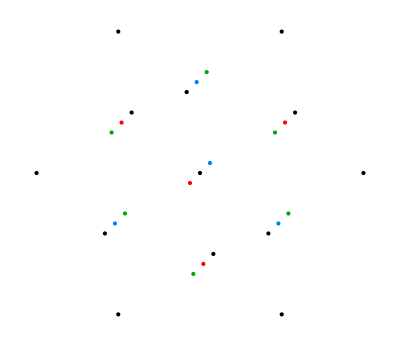
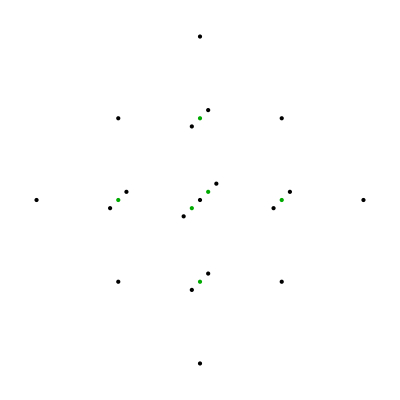

```mathematica
{showgfx[{PointSize[Large],Black,GraphRepRootPoints[{1,3},{1,0,1},gfxprj3d],Red,GraphRepRootPoints[{1,3},{1,0,0},gfxprj3d],grafblue,GraphRepRootPoints[{1,3},{0,0,1},gfxprj3d],grafgreen,GraphRepRootPoints[{1,3},{0,1,0},gfxprj3d]}],showgfx[{PointSize[Large],Black,GraphRepRootPoints[{3,3},{2,0,0},gfxprj3d],grafgreen,GraphRepRootPoints[{3,3},{1,0,0},gfxprj3d]}]}
```

SO(6) D3 ~ SU(4) A3
Vector (1,0,0) 5 - green
Adjoint (0,1,1) 15 - black
Spinor 1 (0,1,0) 4 - red
Spinor 2 (0,0,1) 4 - blue

SO(7) B3
Vector (1,0,0) 6 - yellow
Adjoint (0,1,0) 15 - black
Spinor (0,0,1) 8 - green

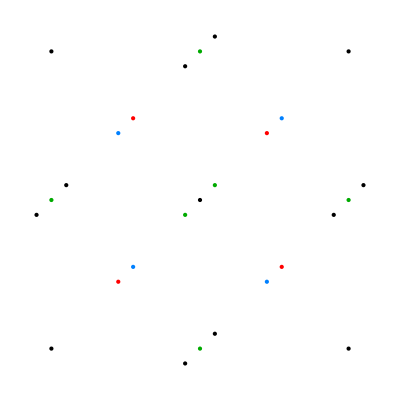
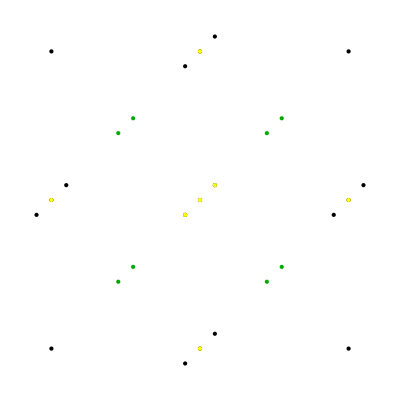

```mathematica
{showgfx[{PointSize[Large],Black,GraphRepRootPoints[{4,3},{0,1,1},gfxprj3d],grafgreen,GraphRepRootPoints[{4,3},{1,0,0},gfxprj3d],PointSize[Large],Red,GraphRepRootPoints[{4,3},{0,1,0},gfxprj3d],grafblue,GraphRepRootPoints[{4,3},{0,0,1},gfxprj3d]}],showgfx[{PointSize[Large],Black,GraphRepRootPoints[{2,3},{0,1,0},gfxprj3d],PointSize[Medium],Yellow,GraphRepRootPoints[{2,3},{1,0,0},gfxprj3d],PointSize[Large],grafgreen,GraphRepRootPoints[{2,3},{0,0,1},gfxprj3d]}]}
```

#### Projected 4D -- the third and fourth dimensions are short lines parallel to the two axes

```mathematica
gfxprj4d = {{1,0},{0,1},{1/8,0},{0,1/8}};
```

SU(5) A4
Fund (1,0,0,0) 5 - red
Fund Conjg (0,0,0,1) 5 - blue
AS (0,1,0,0) 10 - orange
AS Conjg (0,0,1,0) 10 - purple
Adjoint (1,0,1) 24 - black

Sp(8) C4
Fund (1,0,0,0) 6 - green
Adjoint (2,0,0,0) 21 - black

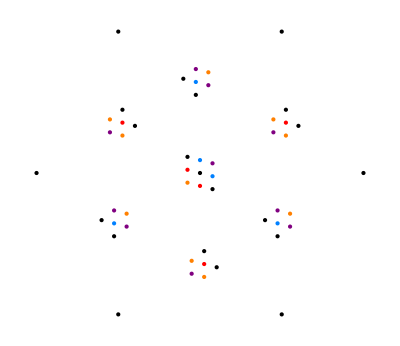
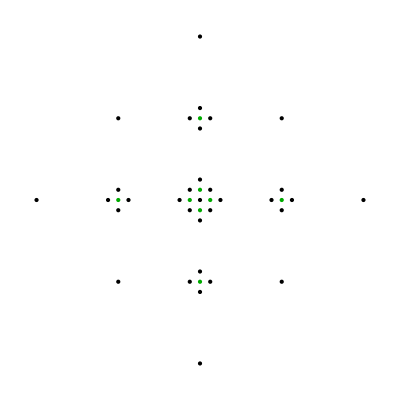

```mathematica
{showgfx[{PointSize[Large],Black,GraphRepRootPoints[{1,4},{1,0,0,1},gfxprj4d],Red,GraphRepRootPoints[{1,4},{1,0,0,0},gfxprj4d],Blend[{Blue,Cyan}],GraphRepRootPoints[{1,4},{0,0,0,1},gfxprj4d],Orange,GraphRepRootPoints[{1,4},{0,1,0,0},gfxprj4d],Purple,GraphRepRootPoints[{1,4},{0,0,1,0},gfxprj4d]}],showgfx[{PointSize[Large],Black,GraphRepRootPoints[{3,4},{2,0,0,0},gfxprj4d],grafgreen,GraphRepRootPoints[{3,4},{1,0,0,0},gfxprj4d]}]}
```

SO(8) D4
Fund (1,0,0,0) 8 - green
Adjoint (0,1,0,0) 28 - black
Spinor 1 (0,0,1,0) 8 - red
Spinor 2 (0,0,0,1) 8 - blue

SO(9) B4
Fund (1,0,0,0) 9 - yellow
Adjoint (0,1,0,0) 36 - black
Spinor (0,0,0,1) 16 - green

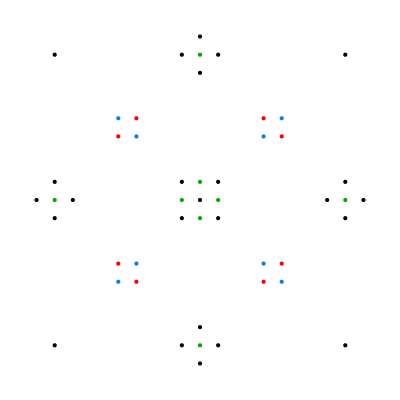
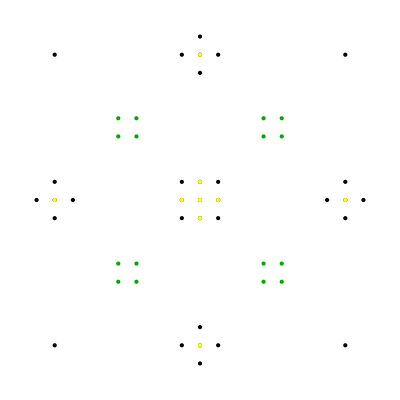

```mathematica
{showgfx[{PointSize[Large],Black,GraphRepRootPoints[{4,4},{0,1,0,0},gfxprj4d],grafgreen,GraphRepRootPoints[{4,4},{1,0,0,0},gfxprj4d],PointSize[Large],Red,GraphRepRootPoints[{4,4},{0,0,1,0},gfxprj4d],grafblue,GraphRepRootPoints[{4,4},{0,0,0,1},gfxprj4d]}],showgfx[{PointSize[Large],Black,GraphRepRootPoints[{2,4},{0,1,0,0},gfxprj4d],PointSize[Medium],Yellow,GraphRepRootPoints[{2,4},{1,0,0,0},gfxprj4d],PointSize[Large],grafgreen,GraphRepRootPoints[{2,4},{0,0,0,1},gfxprj4d]}]}
```

F4
Fund (0,0,0,0) 26 - dark yellow
Adjoint (1,0,0,0) 52 - black

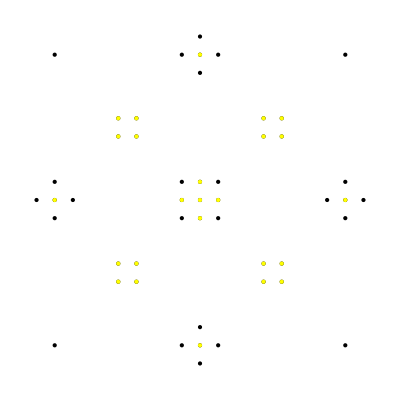

```mathematica
showgfx[{PointSize[Large],Black,GraphRepRootPoints[{6,4},{1,0,0,0},gfxprj4d],PointSize[Medium],Yellow,GraphRepRootPoints[{6,4},{0,0,0,1},gfxprj4d]}]
```